## 1. Define parameters and functions

### 0. Define reaction rates

```mathematica
Clear[xb1,xb2,kT]
xb1=3/2;xb2=2;kT=4012/1000; (*bond length and thermal force*)
kaF[ka_,f_]:=ka*Exp[f*xb1/kT]; (*off rate under force for APC-Ag bond*)
kbF[kb_,f_]:=kb*Exp[f*xb2/kT];(* off rate under force for BCR-Ag bond*)
lamda[ka_,kb_,f_]:=kaF[ka, f]+kbF[kb,f];(*total off rates*)
```

```mathematica
1.0 EulerGamma
```

0.577216

### 1. Time measurement under force

```mathematica
TmeanF[n0_, ka_,kb_,F_]:=Sum[1/(i*lamda[ka,kb,F/i]),{i,1,n0}];(*average litime*)
TvarF[n0_,ka_,kb_,F_]:=Sum[1/(i*lamda[ka,kb,F/i])^2,{i,1,n0}];(*varance lifetime*)
TstdF[n0_,ka_,kb_,F_]:=Sqrt[TvarF[n0,ka,kb,F]]/TmeanF[n0,ka,kb,F];(*std of lifetime distribution, scaled by Tmean*)
TsensF[n0_,ka_,kb_,F_]:=Sum[kbF[kb,F/i]/(i*(lamda[ka,kb,F/i])^2),{i,1,n0}]; (*sensitivity, d Tmean / dEb*)
TvarSensF[n0_, ka_, kb_, F_]:=Sum[2*kbF[kb,F/i]/(i^2 * (lamda[ka, kb, F/i]^3)), {i, 1, n0}]

(*fisher information in cluster lifetime under force F*)
Clear[TimeFisherInfo]
(*TimeFisherInfo[n0_,ka_,kb_,F_]:=N[(TsensF[n0,ka,kb,F]/Sqrt[TvarF[n0,ka,kb,F]])^2,10];*)
TimeFisherInfo[n0_,ka_,kb_,F_, coeff_:0]:=N[(TsensF[n0,ka,kb,F]^2+coeff TvarSensF[n0, ka,kb, F]^2/(2TvarF[n0, ka,kb,F]))/TvarF[n0,ka,kb,F],10];
TimeFisherInfoS0[n0_, ka_, kb_, F_, s0_:0]:=(TsensF[n0,ka,kb,F])^2/(TvarF[n0,ka,kb,F] + s0^2);

(*if independent extraction*)
(*TimeFisherInfoIndepF[n0_, ka_, kb_,f_]:=(Sum[kbF[kb,f]/(i*(lamda[ka,kb,f])^2),{i,1,n0}]/Sqrt[Sum[1/(i*lamda[ka,kb,f])^2,{i,1,n0}]])^2*)
TimeFisherInfoIndepF[n0_, ka_, kb_,f_]:=If[n0==1,(kbF[kb, f]^2/lamda[ka,kb,f]^2) ,If[n0==2, (4 Zeta[3]-3)(kbF[kb, f]^2/lamda[ka,kb,f]^2) ,(kbF[kb, f]^2/lamda[ka,kb,f]^2) * (1+1/(6 (-2+n0) (-1+n0)^2)n0 (6+6 (-2+EulerGamma) EulerGamma (-1+n0)^2+(-1+n0)^2 π^2+6 (-1+n0)^2 PolyGamma[0,n0] (-2+2 EulerGamma+PolyGamma[0,n0])-6 PolyGamma[1,-1+n0]-6 (-2+n0) n0 PolyGamma[1,-1+n0]))]]
TimeFisherInfoIndepFS0[n0_, ka_, kb_,f_, s0_:0]:=(Sum[kbF[kb,f]/(i*(lamda[ka,kb,f])^2),{i,1,n0}])^2/(Sum[1/(i*lamda[ka,kb,f])^2,{i,1,n0}]+s0^2)
```

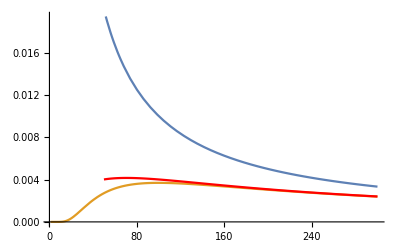

```mathematica
Show[
Plot[{1 /(i lamda[0.0001,1,0/i]), 1 /(i lamda[0.0001,1,200/i])}, {i,1,300}, Filling->False],
Plot[1/((i+200*2/kT+0.5*(200*2/kT)^2/i)lamda[0.0001, 1, 0]),{i, 200/kT, 300}, PlotStyle->Red]
]
```

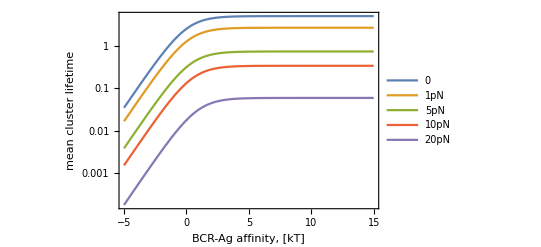

```mathematica
Show[LogPlot[{TmeanF[100, 1, Exp[-ebx], 0],TmeanF[100, 1, Exp[-ebx], 10],TmeanF[100, 1, Exp[-ebx], 100],TmeanF[100, 1, Exp[-ebx], 200],TmeanF[100, 1, Exp[-ebx], 500]

}, {ebx, -5, 15},Frame->True, FrameStyle->Directive[20],
PlotLegends->Placed[{"0", "1pN", "5pN", "10pN", "20pN"}, {0.8, 0.3}]],
FrameLabel->{"BCR-Ag affinity, [kT]", "mean cluster lifetime"}]
```

```mathematica
Integrate[1/(u^2 (Exp[a/u]+Exp[b/u])^2), {u, 0, 1}]
```

∫_0^1 1/((ⅇ^(a/u)+ⅇ^(b/u))^2 u^2)ⅆu

```mathematica
Integrate[1/(u^2 (Exp[a/u])^2), {u, 0, 1}]
```

ConditionalExpression[ⅇ^(-2 a)/(2 a), Re[a]>0]

```mathematica
Clear[a,b];
(*a=1;b=1;*)
Integrate[1/(u Exp[b/u]),{u,0,1}]
```

ConditionalExpression[Gamma[0,b], Re[b]≥0]

```mathematica
Integrate[1/(u Exp[b/u]),{u,0,1}]
```

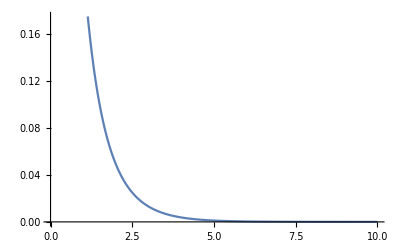

```mathematica
Plot[Gamma[0,x],{x, 0, 10}]
```

```mathematica
i/(i^2 + i0 i +i0^2/2)
```

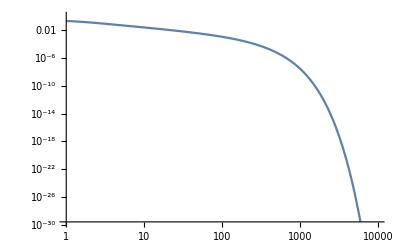

```mathematica
LogLogPlot[TvarF[100, 1, 1, fi],{fi, 1, 10000}]
```

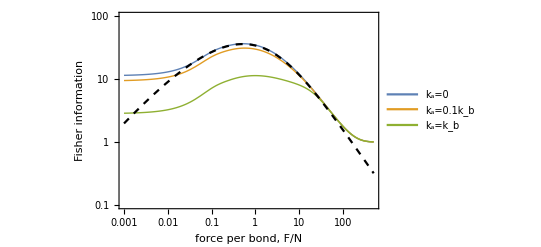

```mathematica
Show[LogLogPlot[{TimeFisherInfo[40,0,1,40fi],TimeFisherInfo[40,0.1,1,40fi], TimeFisherInfo[40,1,1,40fi](*2*40 (fi*1.5/kT) Exp[2 fi*1.5/kT] Gamma[0, fi*(3-2)/kT]^2(1/1)*)

},{fi, 0.001, 500}, PlotRange->{0.1, 100}, PlotStyle->Thick, 
PlotLegends->Placed[{"k_a=0", "k_a=0.1k_b", "k_a=k_b" }, {0.5, 0.4}]],
LogLogPlot[2*40 (fi*2/kT) Exp[2 fi*2/kT] Gamma[0, fi*2/kT]^2, {fi, 0.001, 500}, PlotStyle->{Black, Dashed}],
Frame->True,
FrameLabel->{"force per bond, F/N", "Fisher information"},
FrameStyle->Directive[15]
]
```

General::munfl: 2.63237×10^110 5.48227994862542×10^-332 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

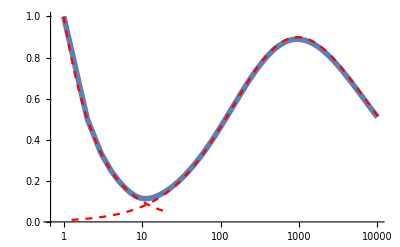

```mathematica
func=TimeFisherInfo;numComp=1;
Show[
ListLogLinearPlot[Join[
Table[{n0x, numComp*func[n0x, 1, Exp[5], 500]/n0x}, {n0x, 1,100, 1}],
Table[{n0x,numComp* func[n0x, 1, Exp[5], 500]/n0x}, {n0x, 100,1000, 20}],
Table[{n0x, numComp*func[n0x, 1, Exp[5], 500]/n0x}, {n0x, 1000,10000, 200}]
],Joined->True, PlotStyle->Thickness[0.01]],LogLinearPlot[{2* ((500/ni)*2/kT) Exp[2 (500/ni)*2/kT] Gamma[0, (500/ni)*2/kT]^2},{ni, 1, 10000}, PlotRange->{0.01, 2}, PlotStyle->{ {Red, Dashed}}],
LogLinearPlot[1/ni, {ni, 1, 20}, PlotStyle->{Red, Dashed}]

]
```

```mathematica
FindMaximum[{b Exp[2b] Gamma[0, b]^2, b>0}, {b, 2}]
```

{0.44956,{b→0.258947}}

```mathematica
ff[b_]:=-2 ⅇ^b Gamma[0,b]+ⅇ^(2 b) Gamma[0,b]^2+2 b ⅇ^(2 b) Gamma[0,b]^2
```

```mathematica
ff[1.0]
```

-0.125804

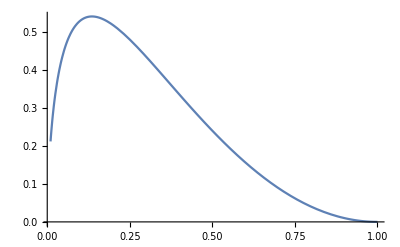

```mathematica
Plot[x Log[x]^2, {x, 0.01, 1}]
```

```mathematica
TimeFisherInfo[11, 1, Exp[2], 500]*1000/11
TimeFisherInfoIndepF[2, 1, 1.0, 0]
TimeFisherInfoIndepF[3, 1, 1.0, 0]
```

112.9383636

0.452057

0.625

```mathematica
Log[1000]^2 / (2.0)^2
```

11.9293

```mathematica
Clear[ka, kb, n0, f]
TimeFisherInfoIndepF[n0, ka, kb,f]
```

(kb^2 (1+(n0 ((-2+EulerGamma) EulerGamma+π^2/6+PolyGamma[0,n0] (2 (-1+EulerGamma)+PolyGamma[0,n0])-6 PolyGamma[1,n0]))/(-2+n0)))/(ka+kb)^2

```mathematica
(EulerGamma-2)EulerGamma + Pi^2/6.0
```

0.823681

```mathematica
Series[PolyGamma[1, x], {x, Infinity, 3}]
```

1/x+1/(2 x^2)+1/(6 x^3)+O[1/x]^4

```mathematica
PolyGamma[1,100]
```

-7947057377592972175046194813599432986939836504926551426326272813841737896458766881/4860930722171905152948289883363115720809877919978731208913601773527589930826240000+π^2/6

```mathematica
Integrate[2 Exp[-t](1-Exp[-t]) t, {t, 0, Infinity}]
```

3/2

```mathematica
Integrate[2 Exp[-t](1-Exp[-t]) t Exp[-t]/(1-Exp[-t]), {t, 0, Infinity}]
```

1/2

```mathematica
Integrate[2 Exp[-t](1-Exp[-t]) t^2 Exp[-t]/(1-Exp[-t])^2, {t, 0, Infinity}]
```

4 (-1+Zeta[3])

```mathematica
Clear[n];
Integrate[(n Exp[-t]-1) n t Exp[-t](1-Exp[-t])^(n-2),t]
```

-(1-ⅇ^-t)^n n (1/n-t/(-1+ⅇ^t))

```mathematica
Integrate[n0(n0-1) t^2 Exp[-2t](1-Exp[-t])^(n0-3), {t, 0, Infinity}]
```

ConditionalExpression[(n0 (6+6 (-2+EulerGamma) EulerGamma (-1+n0)^2+(-1+n0)^2 π^2+6 (-1+n0)^2 PolyGamma[0,n0] (-2+2 EulerGamma+PolyGamma[0,n0])-6 PolyGamma[1,-1+n0]-6 (-2+n0) n0 PolyGamma[1,-1+n0]))/(6 (-2+n0) (-1+n0)^2), Re[n0]>0]

```mathematica
FullSimplify[1/(6 (-2+n) (-1+n)^2)n (6 (-2+EulerGamma) EulerGamma (-1+n)^2+6 (-1+n)^2 PolyGamma[0,n] (-2+2 EulerGamma+PolyGamma[0,n])-6 PolyGamma[1,-1+n]-6 (-2+n) n PolyGamma[1,-1+n])]
```

(n ((-2+EulerGamma) EulerGamma+PolyGamma[0,n] (-2+2 EulerGamma+PolyGamma[0,n])-PolyGamma[1,-1+n]))/(-2+n)

```mathematica
ExpandAll[%]
```

(6 n)/(-12+30 n-24 n^2+6 n^3)-(12 EulerGamma n)/(-12+30 n-24 n^2+6 n^3)+(6 EulerGamma^2 n)/(-12+30 n-24 n^2+6 n^3)+(24 EulerGamma n^2)/(-12+30 n-24 n^2+6 n^3)-(12 EulerGamma^2 n^2)/(-12+30 n-24 n^2+6 n^3)-(12 EulerGamma n^3)/(-12+30 n-24 n^2+6 n^3)+(6 EulerGamma^2 n^3)/(-12+30 n-24 n^2+6 n^3)+(n π^2)/(-12+30 n-24 n^2+6 n^3)-(2 n^2 π^2)/(-12+30 n-24 n^2+6 n^3)+(n^3 π^2)/(-12+30 n-24 n^2+6 n^3)-(12 n PolyGamma[0,n])/(-12+30 n-24 n^2+6 n^3)+(12 EulerGamma n PolyGamma[0,n])/(-12+30 n-24 n^2+6 n^3)+(24 n^2 PolyGamma[0,n])/(-12+30 n-24 n^2+6 n^3)-(24 EulerGamma n^2 PolyGamma[0,n])/(-12+30 n-24 n^2+6 n^3)-(12 n^3 PolyGamma[0,n])/(-12+30 n-24 n^2+6 n^3)+(12 EulerGamma n^3 PolyGamma[0,n])/(-12+30 n-24 n^2+6 n^3)+(6 n PolyGamma[0,n]^2)/(-12+30 n-24 n^2+6 n^3)-(12 n^2 PolyGamma[0,n]^2)/(-12+30 n-24 n^2+6 n^3)+(6 n^3 PolyGamma[0,n]^2)/(-12+30 n-24 n^2+6 n^3)-(6 n PolyGamma[1,-1+n])/(-12+30 n-24 n^2+6 n^3)+(12 n^2 PolyGamma[1,-1+n])/(-12+30 n-24 n^2+6 n^3)-(6 n^3 PolyGamma[1,-1+n])/(-12+30 n-24 n^2+6 n^3)

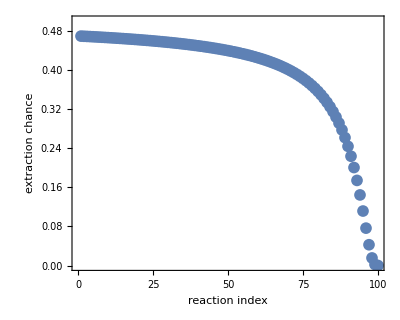

```mathematica
DiscretePlot[1/(1+Exp[100/(8.024(100-m+1))]), {m, 1, 100}, Filling->False, Frame->True, PlotRange->{0, 0.5},FrameLabel->{"reaction index", "extraction chance"}, PlotRange->All, AspectRatio->0.8, FrameStyle->Directive[20], PlotMarkers->{Automatic, 12}]
```

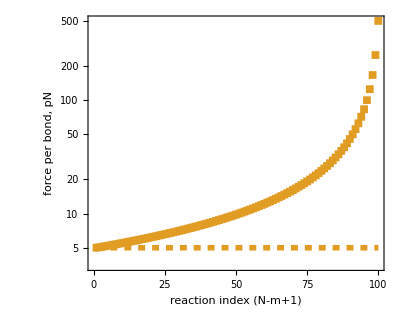

```mathematica
Show[
ListLogPlot[{{None}, Table[{m,500/(100-m+1)}, {m, 1, 100}]},PlotMarkers->{Automatic, 8},PlotRange->All,
 Filling->False],
LogPlot[{None, 5},{m,1,100}, PlotStyle->{{Black},{Dashed, Thickness[0.01]}}],
 Frame->True, FrameLabel->{"reaction index (N-m+1)", "force per bond, pN"}, AspectRatio->0.8, FrameStyle->Directive[22]
]
```

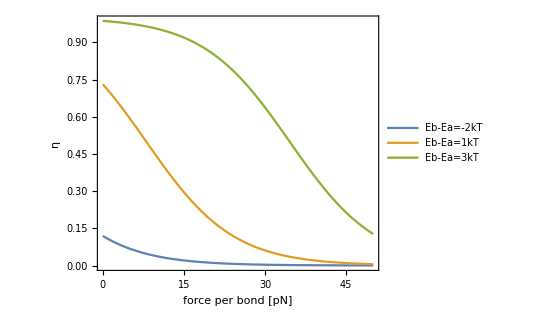

```mathematica
Plot[{1/(1+Exp[2+f/8.024]), 1/(1+Exp[-1+f/8.024]), 1/(1+0.1Exp[-2+f/8.024])}, {f, 0, 50}, Frame->True,PlotLegends->Placed[{"Eb-Ea=-2kT", "Eb-Ea=1kT", "Eb-Ea=3kT"}, {0.8, 0.8}],FrameStyle->Directive[20], FrameLabel->{ "force per bond [pN]", "η"}, AspectRatio->0.8]
```

### 2. Time measurement with rebinding

```mathematica
TmeanOn[n0_, ka_, kb_, k0_]:=Sum[(1+k0/(ka+kb))^(i-1)/i,{i,1,n0}]/(ka+kb);
TvarOn[n0_,ka_, kb_, k0_]:=Module[{},
Clear[gam, lmd, ret];
lmd=ka+kb;
gam=k0/lmd;
ret= ((Sum[Binomial[n0, i]gam^i /i,{i,1,n0}])^2 +
 2Sum[Binomial[n0, i]gam^i/i^2,{i,1,n0}]+
Sum[1/i^2,{i,1,n0}])/(ka+kb+k0)^2;
(*ret= (Sum[(Binomial[n0, i]gam^i /i+1/i)^2,{i,1,n0}])/(ka+kb+k0)^2;*)
Clear[gam, lmd];
ret
];
TstdOn[n0_,ka_, kb_, k0_]:=Sqrt[TvarOn[n0,ka, kb, k0]]/TmeanOn[n0,ka, kb, k0];

TsensOn[n0_, ka_, kb_, k0_]:=Module[{},
Clear[gam,  ret];
gam=k0/( ka+kb);
ret = (kb/(ka+kb)) * (1+ gam*Sum[(1-1/i)(1+gam)^(i-2),{i,2,n0}]/Sum[(1+gam)^(j-1)/j,{j,1,n0}]);
Clear[gam];
ret
]

TimeFisherInfoOn[n0_, ka_, kb_, k0_]:=(TsensOn[n0, ka, kb, k0]/TstdOn[n0, ka, kb, k0])^2;
```

```mathematica
TimeFisherInfoOn[100, 1, 1, 1]*1.0
```

277.418

### 2. Antigen number measurement under force

```mathematica
xb1=1.5;xb2=2.0;kT=4.012;
nMeanF[n0_,ka_,kb_,F_]:=Sum[1/(1+kbF[kb,F/i]/kaF[ka, F/i]),{i,1, n0}];
nVarF[n0_,ka_,kb_,F_]:=Sum[kbF[kb,F/i]kaF[ka, F/i]/(kbF[kb,F/i]+kaF[ka, F/i])^2, {i, 1, n0}];
nStdF[n0_,ka_,kb_,F_]:=Sqrt[Sum[kbF[kb,F/i]kaF[ka, F/i]/(kbF[kb,F/i]+kaF[ka, F/i])^2, {i, 1, n0}]];
nSensF[n0_,ka_,kb_,F_]:=nVarF[n0,ka,kb,F];

(*Fisher information in n_ag*)
NagFisherInfo[n0_Integer,ka_,kb_,F_]:=Sqrt[nVarF[n0,ka,kb,F]]^2
NagFisherInfoS0[n0_Integer,ka_,kb_,F_, s0_:1]:=nVarF[n0,ka,kb,F]^2/(nVarF[n0,ka,kb,F]+s0)
(*if independent extraction*)
NagFisherInfoIndepF[n0_, ka_, kb_, F_]:=(Sqrt[kaF[ka, F] kbF[kb, F] n0]/(kaF[ka, F]+kbF[kb, F]))^2;
NagFisherInfoIndepFS0[n0_, ka_, kb_, F_, s0_:1]:=(kaF[ka, F] kbF[kb, F] n0/(kaF[ka, F]+kbF[kb, F])^2)^2/(kaF[ka, F] kbF[kb, F] n0/(kaF[ka, F]+kbF[kb, F])^2+s0^2);
```

```mathematica
NagFisherInfo[100, 1, 1, 0]
```

25.

```mathematica
ArgMax[{NagFisherInfo[n,1,0.01, 200]/n, n>1}, n, Integers]
```

8

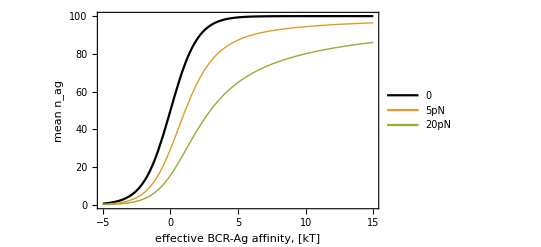

```mathematica
Show[Plot[{nMeanF[100, 1, Exp[-ebx], 0],nMeanF[100, 1, Exp[-ebx-5/8.024], 500],nMeanF[100, 1, Exp[-ebx-20/8.024], 2000]

}, {ebx, -5, 15},Frame->True, FrameStyle->Directive[20],PlotRange->{0, 100},PlotStyle->{{Black}, {Thick}, {Thick}},
PlotLegends->Placed[{"0", "5pN",  "20pN"}, {0.12, 0.6}]],
(*Plot[{nMeanF[100, 1, Exp[-ebx], 0],nMeanF[100, 1, Exp[-ebx+5/8.024], 0],nMeanF[100, 1, Exp[-ebx+20/8.024], 0]},{ebx, -5, 15}, PlotStyle->Dashed],*)
(*Plot[nMeanF[100, 1, Exp[-ebx], 0],{ebx, -5, 15}, PlotStyle->Black],*)
FrameLabel->{"effective BCR-Ag affinity, [kT]", "mean n_ag"}]
```

General::munfl: 1.77367×10^108 8.14307620123853×10^-330 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.14592×10^216 1.45937511376004×10^-654 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.77367×10^108 8.14307620123853×10^-330 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

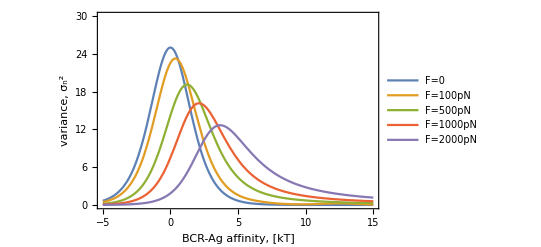

```mathematica
Plot[{nVarF[100, 1, Exp[-ebx], 0],nVarF[100, 1, Exp[-ebx], 100],nVarF[100, 1, Exp[-ebx], 500],nVarF[100, 1, Exp[-ebx], 1000],nVarF[100, 1, Exp[-ebx], 2000]

}, {ebx, -5, 15},Frame->True, FrameStyle->Directive[20],PlotRange->{0, 30},
PlotLegends->Placed[{"F=0", "F=100pN", "F=500pN", "F=1000pN", "F=2000pN"}, {0.8, 0.6}],
FrameLabel->{"BCR-Ag affinity, [kT]", "variance, σ_n^2"}]
```

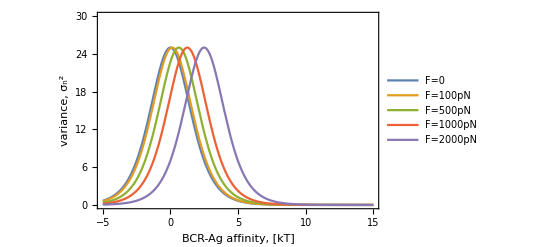

```mathematica
Plot[{nVarF[100, 1, Exp[-ebx], 0],nVarF[100, 1, Exp[-ebx+1*0.5/kT], 0],nVarF[100, 1, Exp[-ebx+5*0.5/kT], 0],nVarF[100, 1, Exp[-ebx+10*0.5/kT], 0],nVarF[100, 1, Exp[-ebx+20*0.5/kT], 0]

}, {ebx, -5, 15},Frame->True, FrameStyle->Directive[20],PlotRange->{0,30},
PlotLegends->Placed[{"F=0", "F=100pN", "F=500pN", "F=1000pN", "F=2000pN"}, {0.8, 0.6}],
FrameLabel->{"BCR-Ag affinity, [kT]", "variance, σ_n^2"}]
```

General::munfl: 2.36217×10^162 4.59107397031862×10^-438 is too small to represent as a normalized machine number; precision may be lost.

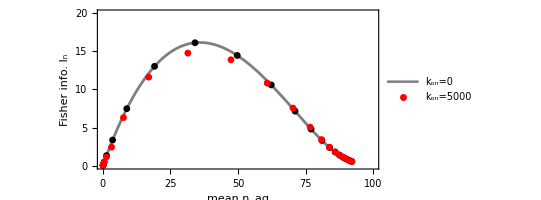

```mathematica
n0=100;N0=n0;
Show[ParametricPlot[{
(*{nMeanF[n0, 1, Exp[-ebx], 0],NagFisherInfo[n0, 1, Exp[-ebx], 0]},*)
(*{nMeanF[n0, 1, Exp[-ebx], n0],NagFisherInfo[n0, 1, Exp[-ebx], n0]},
{nMeanF[n0, 1, Exp[-ebx], 5n0],NagFisherInfo[n0, 1, Exp[-ebx], 5n0]},*)
{nMeanF[n0, 1, Exp[-ebx], 10n0],NagFisherInfo[n0, 1, Exp[-ebx], 10n0]}
}, {ebx, -5, 15},Frame->True, FrameStyle->Directive[20],PlotRange->{{0, n0}, {0, 20}},PlotStyle->{{Gray, Thickness[0.005]}, {Red, Thickness[0.005]}},
PlotLegends->Placed[{"k_on=0"}, {0.4, 0.4}]
(*PlotLegends->Placed[{"0", "10pN", "5pN", "10pN", "20pN"}, {0.4, 0.2}]*)],
ListPlot[Table[{findNMean[Exp[-ebx], 10.0 n0, 0], findInfo[n0, Exp[-ebx], 10.0 n0, 0]}, {ebx, -5, 15, 1}],PlotStyle->Black, PlotMarkers->{Automatic, Small}],
ListPlot[Table[{findNMean[Exp[-ebx], 10.0 n0, 5000], findInfo[n0, Exp[-ebx], 10.0 n0, 5000]}, {ebx, -5, 15, 1}], PlotStyle->Red, PlotMarkers->{Automatic, Small},PlotLegends->Placed[{"k_on=5000"}, {0.4, 0.2}]],
AspectRatio->0.5,
FrameLabel->{"mean n_ag", "Fisher info. I_n"}]
```

## 2. Making Figures

```mathematica
colorlist =Join[ ColorData[99, "ColorList"], ColorData[100, "ColorList"]]
```

{RGBColor[0.65, 0., 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.461492, 0.563303, 0.0104797],RGBColor[0.659814, 0.212037, 0.300311],RGBColor[0.212151, 0.39271, 0.8],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.6478640450004207, 0.3082039324993689, 0.019660112501051874],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.6531262919989895, 0.2133747416002021, 0.31145618000168407],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278],RGBColor[0.0684356, 0.645252, 0.782123],RGBColor[0.98993, 0.699651, 0.0271887],RGBColor[0.450866, 0.379481, 1.],RGBColor[0.369422, 0.7, 0.229826],RGBColor[0.942659, 0.463296, 0.151884],RGBColor[0.214511, 0.528391, 0.957413],RGBColor[0.827693, 0.730855, 0.],RGBColor[0.546532, 0.322857, 0.883671],RGBColor[0.0575287, 0.697632, 0.634101],RGBColor[0.971874, 0.609371, 0.0759396],RGBColor[0.24027755634958686, 0.5134535951530563, 0.9542792262231498],RGBColor[0.664468179450943, 0.7160576871329034, 0.038246733312056906],RGBColor[0.5359107296880482, 0.3292005458464977, 0.8879524511010058],RGBColor[0.09300232680379224, 0.6615923955711573, 0.7003478159388691],RGBColor[0.9875991060491971, 0.716733028919815, 0.01761147689957558]}

```mathematica
colorlist =Join[{Black},Table[ ColorData["Rainbow"][i], {i, 0, 1, 1/4}]]
```

{GrayLevel[0],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
colorlist =Table[ ColorData["Rainbow"][i], {i, 0, 1, 1/4}]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

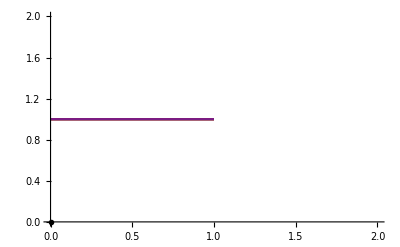

```mathematica
Plot[{1,1,1,1,1, 1},{x,0,1},PlotRange->{{0, 2}, {0,2}}, PlotStyle->colorlist, PlotLegends->Placed[{"-2", "0", "2", "5", "10"},{0.8, 0.6}]]
```

### 2.1 Plot Fisher info against BCR affinity

```mathematica
Clear[MakePlot];
MakePlot[n0_, ka_, f_, i_, func_]:=
Module[{}, LogPlot[func[n0, ka, 1/Exp[kbx], n0*f]/n0, {kbx, -3, 10}, PlotStyle->colorlist[[i]], PlotRange->{0.01, 1}]]
MakePlotEffDeltaE[n0_, ka_, f_, i_, func_]:=
Module[{}, LogPlot[func[n0, ka, 1/Exp[kbx+f*(xb2-xb1)/kT], n0*f], {kbx, -3, 10}, PlotStyle->{colorlist[[i]], Thickness[0.008]}, PlotRange->{0.1, 100}]]
```

General::munfl: 1.77367×10^108 5.37441200732451×10^-327 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.36406×10^163)^2) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

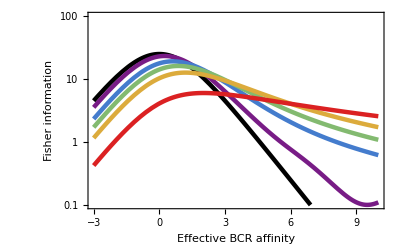

```mathematica
n01= 100;ka1=1;func =NagFisherInfo; (*change func to TimeFisherInfo to plot curves for time*)
fList = {0, 1, 5, 10,20, 80};
pList={};
For[i=1,i≤ Length[fList],i++,
AppendTo[pList, MakePlotEffDeltaE[n01, ka1, fList[[i]], i, func]]];
Show[
Sequence@@pList,
(*LogPlot[20*0.5/(4.012(x^2)),{x,2, 40}, PlotStyle->Dashed],*)
(*LogPlot[{-1,-1,-1,-1,-1}, {x,-4,4}, PlotStyle->colorlist, PlotLegends->Placed[fList, {0.8, 0.6}]],
*)
Frame->True,
FrameLabel->{"Effective BCR affinity", "Fisher information"},
FrameStyle->Directive[16]
]
```

```mathematica
ContourPlot[2x+1,
{x,0,4Pi},{y,0,4 Pi},PlotLegends->Automatic,Contours->6, ColorFunction->colorlist]
```

General::munfl: 1.77367×10^108 4.44469759635634×10^-328 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((4.74328×10^163)^2) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

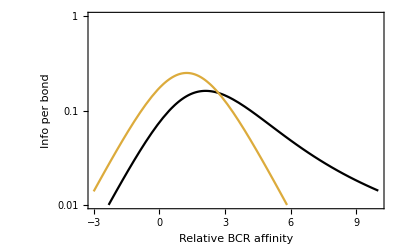

```mathematica
Show[
MakePlot[100, ka1, 10, 1, NagFisherInfo],
MakePlot[100, ka1, 10/100, 5, NagFisherInfoIndepF],
Frame->True,
FrameLabel->{"Relative BCR affinity", "Info per bond"},
FrameStyle->Directive[16]
]
```

### 2.2 Plot Fisher info against total force

```mathematica
Clear[MakePlotF];
MakePlotF[n0_, ka_, kb_, i_, func_]:=Module[{}, LogLogPlot[func[n0, ka, kb, Rationalize[fx]*n0], {fx, 0.001, 10000}, PlotStyle->colorlist[[i]], PlotRange->{0.1, 100}, PlotLegends->Log[kb]]]

MakePlotFList[n0_, ka_, kb_, i_, func_]:=Module[{}, ListLogLogPlot[
Join[
Table[{fx, func[n0, ka, kb, Rationalize[fx]*n0]}, {fx, 0.001, 0.01, 0.001}],
Table[{fx, func[n0, ka, kb, Rationalize[fx]*n0]}, {fx, 0.01, 1, 0.01}],
Table[{fx, func[n0, ka, kb, Rationalize[fx]*n0]}, {fx, 1, 100, 1}],
Table[{fx, func[n0, ka, kb, Rationalize[fx]*n0]}, {fx,100, 1000, 10}],
Table[{fx, func[n0, ka, kb, Rationalize[fx]*n0]}, {fx,1000, 10000, 100}]
]
, PlotStyle->colorlist[[i]], PlotRange->{0.1, 100},  Joined->True]]

MakePlotFListEff[n0_, ka_, kb_, i_, func_]:=Module[{}, ListLogLogPlot[
Join[
Table[{fx, func[n0, ka, kb Exp[-fx (xb2-xb1)/kT], Rationalize[fx]*n0]}, {fx, 0.001, 0.01, 0.001}],
Table[{fx, func[n0, ka, kb Exp[-fx (xb2-xb1)/kT], Rationalize[fx]*n0]}, {fx, 0.01, 1, 0.01}],
Table[{fx, func[n0, ka, kb Exp[-fx (xb2-xb1)/kT], Rationalize[fx]*n0]}, {fx, 1, 100, 1}],
Table[{fx, func[n0, ka, kb Exp[-fx (xb2-xb1)/kT], Rationalize[fx]*n0]}, {fx,100, 1000, 10}]
(*Table[{fx, func[n0, ka, kb Exp[-fx (xb2-xb1)/kT], Rationalize[fx]*n0]}, {fx,1000, 10000, 20}]*)
],
PlotStyle->colorlist[[i]], PlotRange->{0.01, 100},  Joined->True]]
MakePlotFDashed[n0_, ka_, kb_, i_, func_]:=Module[{}, LogLogPlot[func[n0, ka, kb, fx*n0]/n0, {fx, 0.001, 10000}, PlotStyle->{colorlist[[i]], Dashed}, PlotRange->{0.001, 1}]]
```

```mathematica
TimeFisherInfoApprox[n0_, ka_, kb_, F_]:=Module[{}, 
Clear[xbar, i0];
xbar = (xa*ka + xb*kb)/(ka+kb);
i0=F xbar/kT;
If[i0<n0,
ret = 2i0 (n0+1-i0)/(n0+1-i0) Log[(n0+i0)/(2i0)]^2/(1+ka/kb)^2,ret=3/(1+ka Exp[-F(xb-xa)/(n0 kT)]/kb)^2];
Clear[xbar, i0];
ret
]
TimeFisherInfoApprox[100, 1, 1, 500.0]
```

1.27113

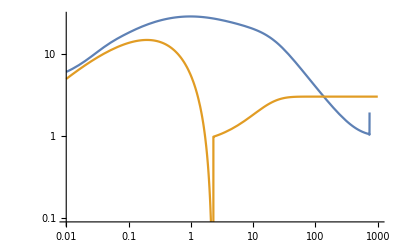

```mathematica
LogLogPlot[{ 
TimeFisherInfo[100, 1, 1, fx*100],
TimeFisherInfoApprox[100, 1, 1, fx*100]
},{fx, 0.01, 1000} ]
```

```mathematica
N[NagFisherInfo[100, Exp[-5], Exp[-5000/kT], Rationalize[10000]*100], 5]
```

0.0066481

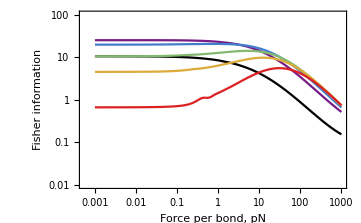

```mathematica
n01= 100;ka1=1; func=NagFisherInfo;plot=MakePlotFListEff;
Show[
plot[n01, ka1,Exp[2]ka1, 1,func],(*change func to TimeFisherInfo to plot curves for time*)
plot[n01, ka1, ka1, 2, func],
plot[n01, ka1, Exp[-1]ka1, 3, func],
plot[n01, ka1, Exp[-2]ka1, 4, func],
plot[n01, ka1, Exp[-3]ka1, 5, func],
plot[n01, ka1, Exp[-5]ka1, 6, func],
Frame->True,
FrameLabel->{"Force per bond, pN", "Fisher information"},
FrameTicksStyle->Directive[12],
FrameStyle->Directive[16]
]
```

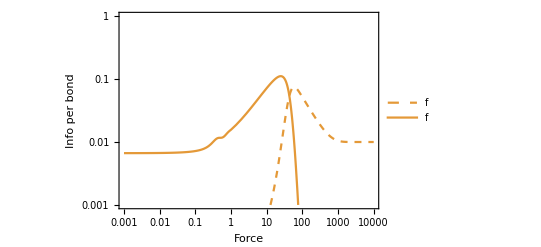

```mathematica
Show[
MakePlotFDashed[n01, ka1,Exp[-5]ka1, 5,TimeFisherInfo],
MakePlotF[n01, ka1, Exp[-5]ka1, 5,  NagFisherInfo],
Frame->True,
FrameLabel->{"Force", "Info per bond"},
FrameTicksStyle->Directive[12],
FrameStyle->Directive[16]
]
```

### 2.3 Plot against kon

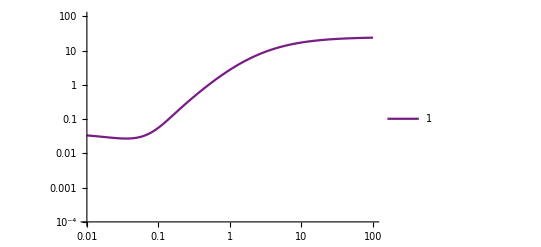

```mathematica
Clear[MakePlotOn];
MakePlotOn[n0_, ka_, kb_, i_]:=Module[{}, 
Show[LogLogPlot[TimeFisherInfoOn[n0, ka, kb, kon]/n0, {kon, 0.01, 100}, PlotStyle->colorlist[[i]], PlotRange->{0.0001, 100}, PlotLegends->{kb}]
(*LogLogPlot[NagFisherInfo[n0, ka, kb, 0]/n0, {kon, 0.01, 100}, PlotStyle->{colorlist[[i]], Dashed}, PlotRange->{0.0001, 100}]*)
]
]
MakePlotOn[100, 1, 1, 1]
```

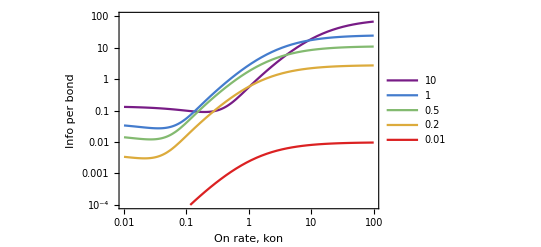

```mathematica
n01= 100;ka1=1; 
Show[
MakePlotOn[n01, ka1,10ka1, 1],(*change func to TimeFisherInfo to plot curves for time*)
MakePlotOn[n01, ka1, ka1, 2],
MakePlotOn[n01, ka1, 0.5ka1, 3],
MakePlotOn[n01, ka1, 0.2ka1, 4],
MakePlotOn[n01, ka1, 0.01ka1, 5],
Frame->True,
FrameLabel->{"On rate, kon", "Info per bond"},
FrameTicksStyle->Directive[12],
FrameStyle->Directive[16]
]
```

### 2.4 Plot against cluster size

```mathematica
numComp = 1;
```

```mathematica
Clear[MakePlotN];
(*colorlist = Table[ ColorData["AvocadoColors"][i], {i, 4/5, 0, -1/5}]*)
MakePlotN[ ka_, kb_, f_,i_, func_]:=Module[{}, ListLogLogPlot[

Join[
Table[{n0x, numComp*func[n0x, ka, kb , f]/n0x}, {n0x, 1,100, 1}],
Table[{n0x, numComp*func[n0x, ka, kb, f]/n0x}, {n0x, 100,1000, 20}],
Table[{n0x,numComp* func[n0x, ka, kb, f]/n0x}, {n0x, 1000,10000, 200}]
],

 PlotStyle->colorlist[[i]], PlotRange->{{1, 10000},{0.001, 10}}, PlotLegends->{f}, Joined->True]]
MakePlotNFixTotal[ ka_, kb_, f_,i_, func_]:=Module[{}, ListLogLinearPlot[
Join[
Table[{n0x, numComp*func[n0x, ka, kb, f]/n0x}, {n0x, 1,100, 1}],
Table[{n0x,numComp* func[n0x, ka, kb, f]/n0x}, {n0x, 100,1000, 20}],
Table[{n0x, numComp*func[n0x, ka, kb, f]/n0x}, {n0x, 1000,3000, 200}]
],

PlotStyle->{colorlist[[i]], Thickness[0.01]}, (*PlotRange->{{1, 3000},{1, 3000}}, *)PlotLegends->{f}, Joined->True]]
MakePlotNFixInitFPerBond[ ka_, kb_, f_,i_, func_]:=Module[{}, ListLogLogPlot[

Join[
Table[{n0x, numComp*func[n0x, ka, kb, f/n0x]/n0x}, {n0x, 1,100, 1}],
Table[{n0x, numComp*func[n0x, ka, kb, f/n0x]/n0x}, {n0x, 100,1000, 20}]
(*Table[{n0x, numComp*func[n0x, ka, kb, f/n0x]/n0x}, {n0x, 1000,10000, 200}]*)
],

PlotStyle->{colorlist[[i]], Thickness[0.008]}, PlotRange->{{1, 1000},{1, 1000}},  Joined->True]]

MakePlotNEff[ ka_, kb_, f_,i_, func_]:=Module[{}, ListLogLogPlot[

Join[
Table[{n0x,numComp*func[n0x, ka, kb Exp[-f*(xb2-xb1)/(n0x*kT)] , f]/n0x}, {n0x, 1,100, 1}],
Table[{n0x,numComp* func[n0x, ka, kb Exp[-f*(xb2-xb1)/(n0x*kT)], f]/n0x}, {n0x, 100,1000, 20}],
Table[{n0x, numComp*func[n0x, ka, kb Exp[-f*(xb2-xb1)/(n0x*kT)], f]/n0x}, {n0x, 1000,10000, 200}]
],

 PlotStyle->colorlist[[i]], PlotRange->{{1, 10000},{0.001, 10}}, PlotLegends->{f}, Joined->True]]

MakePlotNKon[ ka_, kb_, kon_,i_, func_]:=Module[{}, ListLogLogPlot[
Join[
Table[{n0x,numComp* func[n0x, ka Exp[500*1.5/(n0x*4.012)], kb Exp[500*2/(n0x*4.012)], kon]/n0x}, {n0x, 1,100, 1}],
Table[{n0x, numComp*func[n0x, ka Exp[500*1.5/(n0x*4.012)], kb Exp[500*2/(n0x*4.012)], kon]/n0x}, {n0x, 100,1000, 20}](*,
Table[{n0x, func[n0x, ka, kb, kon]/n0x}, {n0x, 1000,10000, 200}]*)
],

PlotStyle->{colorlist[[i]], Thickness[0.008]}, PlotRange->{{1, 1000},{1,10000}}, PlotLegends->{f}, Joined->True]]
```

```mathematica
NagFisherInfo[100, 1, 1,500]
```

14.2084

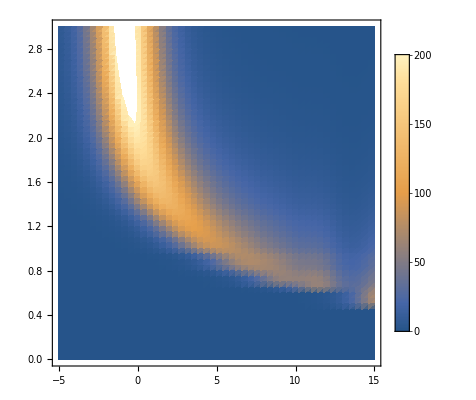

```mathematica
func=NagFisherInfo;

infoTable = 
Table[ 
1000func[Floor[10^n0x],  1, Exp[-ebx] , 500]/(Floor[10^n0x]),{n0x,0,3, 0.05}, {ebx, -5, 20, 0.5}];
ListDensityPlot[infoTable,DataRange->{{-5, 15}, {0, 3}}, PlotRange->{0, 200}, PlotLegends->Automatic]
```

General::munfl: 2.63237×10^110 5.48227994862542×10^-332 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

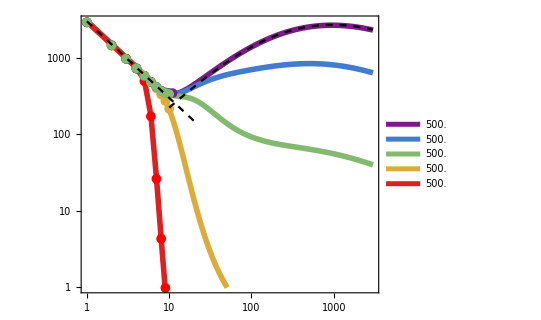

```mathematica
n01= 100;ka1=1; func=TimeFisherInfo;plotFunc =MakePlotNFixTotal;f0=500.0;
Show[
plotFunc[ ka1 , ka1 Exp[5], f0, 1,func],(*change func to TimeFisherInfo to plot curves for time*)
plotFunc[ ka1 , ka1 ,f0, 2, func],
plotFunc[ ka1 , ka1 Exp[-2],f0, 3, func],
plotFunc[ ka1 , ka1 Exp[-5], f0,4, func],
plotFunc[ ka1 ,ka1 Exp[-10],f0, 5, func],
(*plotFunc[ ka1,ka1 Exp[-5],f0, 6, func],*)
(*MakePlotN[n01, ka1, 0.001ka1, 5, func],*)
(*LogLogPlot[1, {x,1, 10000}, PlotStyle->{Gray, Dashed}],*)

(*time, eb=0*)
ListLogLogPlot[
{{1,971.13*numComp/1000},{2,485.565*numComp/1000},{3,323.71*numComp/1000},{4,242.78262*numComp/1000},{5,194.2256*numComp/1000},{6,161.89*numComp/1000},{7,139.13*numComp/1000},{8,123.94*numComp/1000},{9,117.3474*numComp/1000},{10,114.7*numComp/1000}},PlotMarkers->{Automatic, Medium}
],
(*time, eb=10*)
ListLogLogPlot[{{1,971.13*numComp/1000},{2,485.5654*numComp/1000},{3,323.6967*numComp/1000},{4,240.958*numComp/1000},{5,164.92*numComp/1000},{6,57.367*numComp/1000},{7,8.7618*numComp/1000},{8,1.447*numComp/1000},{9,0.329*numComp/1000},{10,0.0972*numComp/1000}}, PlotStyle->Red, PlotMarkers->{Automatic, Medium}],
(*tim, eb=5*)
ListLogLogPlot[{{1,971.13*numComp/1000},{2,485.56*numComp/1000},{3,323.7*numComp/1000},{4,242.77*numComp/1000},{5,194.0*numComp/1000},{6,160.43*numComp/1000},{7,133.7173*numComp/1000},{8,110.308*numComp/1000},{9,90.774*numComp/1000},{10,72.03*numComp/1000}}, PlotStyle->colorlist[[4]],PlotMarkers->{Automatic, Medium}],
(*time, eb=-2*)
ListLogLogPlot[{{1,971.13*numComp/1000},{2,485.5654*numComp/1000},{3,323.71*numComp/1000},{4,242.7827*numComp/1000},{5,194.2269*numComp/1000},{6,161.902*numComp/1000},{7,139.16295*numComp/1000},{8,124.02823*numComp/1000},{9,117.53743*numComp/1000},{10,115.0657*numComp/1000},{11,115.268*numComp/1000}}, PlotStyle->colorlist[[1]],PlotMarkers->{Automatic, Medium}],
(*time eb=2*)
ListLogLogPlot[{{1.0000,971.13*numComp/1000},{2.0000,485.57*numComp/1000},{3.0000,323.71*numComp/1000},{4.0000,242.78*numComp/1000},{5.0000,194.22*numComp/1000},{6.0000,161.83*numComp/1000},{7.0000,138.89*numComp/1000},{8.0000,123.30*numComp/1000},{9.0000,115.96*numComp/1000},{10.000,112.11*numComp/1000}},  PlotStyle->colorlist[[3]],PlotMarkers->{Automatic, Medium}],
LogLogPlot[{numComp* 2* ((f0/ni)*2/kT) Exp[2 (f0/ni)*2/kT] Gamma[0, (f0/ni)*2/kT]^2},{ni, 10, 3000}, PlotStyle->{ {Black, Dashed}}], 

LogLogPlot[{numComp/ni},{ni, 1, 20}, PlotStyle->{ {Black, Dashed}}], 
Frame->True,
AspectRatio->0.8,
(*FrameLabel->{"Cluster size", "Info per bond"},*)
FrameTicksStyle->Directive[20],
FrameStyle->Directive[20]
]
```

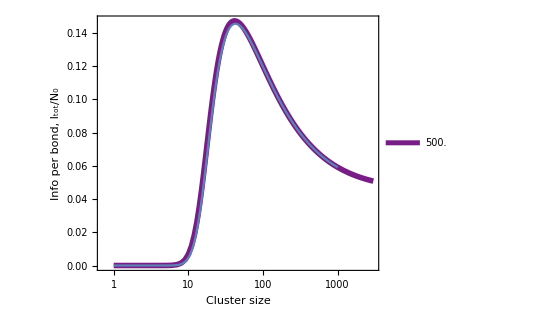

```mathematica
n01= 100;ka1=1; func=NagFisherInfo;plotFunc =MakePlotNFixTotal;f0=500.0;Show[plotFunc[ ka1 , ka1 Exp[-3], f0, 1,func],

LogLinearPlot[NIntegrate[Exp[3-f0*0.5/(4.012u*n)]/(1+Exp[3-f0*0.5/(4.012u*n)])^2, {u, 0, 1}], {n, 1, 1000}],
Frame->True,
AspectRatio->0.8,
FrameLabel->{"Cluster size", "Info per bond, I_tot/N_0"},
FrameTicksStyle->Directive[16],
FrameStyle->Directive[20] ]
```

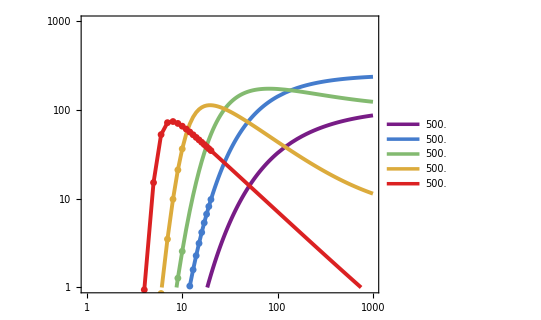

```mathematica
n01= 100;ka1=1; func=NagFisherInfo;plotFunc =MakePlotNFixTotal;f0=500.0;
Show[
plotFunc[ ka1 , ka1 Exp[2], f0, 1,func],(*change func to TimeFisherInfo to plot curves for time*)
plotFunc[ ka1 , ka1 ,f0, 2, func],
plotFunc[ ka1 , ka1 Exp[-2],f0, 3, func],
plotFunc[ ka1 , ka1 Exp[-5], f0,4, func],
plotFunc[ ka1 ,ka1 Exp[-10],f0, 5, func],
(*plotFunc[ ka1,ka1 Exp[-5],f0, 6, func],*)
(*MakePlotN[n01, ka1, 0.001ka1, 5, func],*)
(*LogLogPlot[1, {x,1, 10000}, PlotStyle->{Gray, Dashed}],*)

(*nag, eb=0*)
ListLogLogPlot[{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0.000034880*numComp/6},{7,0.00017084*numComp/7},{8,0.000584*numComp/8},{9,0.00156559*numComp/9},{10,0.00352*numComp/10},{11,0.006961*numComp/11},{12,0.012451*numComp/12},{13,0.02059261*numComp/13},{14,0.031981*numComp/14},{15,0.047183*numComp/15},{16,0.066778*numComp/16},{17,0.091109*numComp/17},{18,0.12060*numComp/18},{19,0.155562*numComp/19},{20,0.19622*numComp/20}}, PlotStyle->colorlist[[2]], PlotMarkers->{Automatic,Small}
],
(*nag, eb=10*)
ListLogLogPlot[{{1,1.9067427211612053*^-20},{2,3.2387045598493876*^-7},{3,0.006992701773334567},{4,0.9419928198936998},{5,15.212512560647676},{6,52.82556129748563},{7,72.08457013615902},{8,74.21063385462084},{9,70.65262490653797},{10,65.79471128495658},{11,60.97477784016462},{12,56.56407688020131},{13,52.63034761537778},{14,49.147095374281},{15,46.06250494352424},{16,43.31322981229337},{17,40.869375707817206},{18,38.679019565489696},{19,36.70660769111651},{20,34.922356913447096}}, PlotStyle->colorlist[[5]], PlotMarkers->{Automatic, Small}],
ListLogLogPlot[{{1,1.2847531396077308*^-22},{2,2.1822219698032243*^-9},{3,0.00004711841741840928},{4,0.006394523659736477},{5,0.11970025540412668},{6,0.8557991353532852},{7,3.504002226177422},{8,9.879999995422828},{9,21.12950329222969},{10,36.496790636070706}}, PlotStyle->colorlist[[4]], PlotMarkers->{Automatic, Small}],

ListLogLogPlot[{{1,6.3964092397472154*^-24},{2,1.0864643440539914*^-10},{3,2.345888499543289*^-6},{4,0.0003183798929382876},{5,0.005965757099425441},{6,0.042941041680901924},{7,0.18007587731467115},{8,0.5374369951639955},{9,1.2733523469944577},{10,2.556645454362931}}, PlotStyle->colorlist[[3]], PlotMarkers->{Automatic, Small}],
Frame->True,
AspectRatio->0.8,
(*FrameLabel->{"Cluster size", "Info per bond"},*)
FrameTicksStyle->Directive[16],
FrameStyle->Directive[20]
]
```

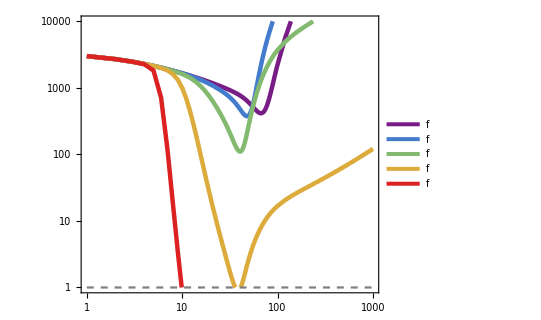

```mathematica
n01= 100;ka1=1; func=TimeFisherInfoOn;plotFunc =MakePlotNKon;f0=10;
Show[
plotFunc[ ka1 , ka1 Exp[2], f0, 1,func],(*change func to TimeFisherInfo to plot curves for time*)
plotFunc[ ka1 , ka1 ,f0, 2, func],
plotFunc[ ka1 , ka1 Exp[-2],f0, 3, func],
plotFunc[ ka1 , ka1 Exp[-5], f0,4, func],
plotFunc[ ka1 ,ka1 Exp[-10],f0, 5, func],
(*plotFunc[ ka1,ka1 Exp[-5],f0, 6, func],*)
(*MakePlotN[n01, ka1, 0.001ka1, 5, func],*)
LogLogPlot[1, {x,1, 10000}, PlotStyle->{Gray, Dashed}],
Frame->True,
AspectRatio->0.8,
(*FrameLabel->{"Cluster size", "Info per bond"},*)
FrameTicksStyle->Directive[16],
FrameStyle->Directive[20]
]
```

```mathematica
infoTableNag= Table[ 
NagFisherInfoIndepF[100, 1, Exp[-ebx],fx], {ebx, -5,15, 0.1}, {fx,0,60, 0.3}];
```

```mathematica
Export[ "/Users/skyhd/Documents/research/synapse/tugOfWar/manuscript/v2.4/data/infoTableNag_Indep.dat",infoTableNag]
```

/Users/skyhd/Documents/research/synapse/tugOfWar/manuscript/v2.4/data/infoTableNag_Indep.dat

```mathematica
(*infoTableTend= Table[ If[
TimeFisherInfo[100, 1, Exp[-ebx],fx]>0.1,If[TimeFisherInfo[100, 1, Exp[-ebx],fx]<30,TimeFisherInfo[100, 1, Exp[-ebx],fx], 30] , None], {ebx, -5,15, 0.5}, {fx,0,6000, 30}];*)
infoTableTend= Table[ TimeFisherInfoIndepF[100, 1.0, Exp[-ebx],fx], {ebx, -5,15, 0.1}, {fx,0,60, 0.3}];
```

```mathematica
Export[ "/Users/skyhd/Documents/research/synapse/tugOfWar/manuscript/v2.4/data/infoTableTend_Indep.dat",infoTableTend]
```

/Users/skyhd/Documents/research/synapse/tugOfWar/manuscript/v2.4/data/infoTableTend_Indep.dat

```mathematica
infoTableTend0= Table[ If[
TimeFisherInfo[100, 1, Exp[-ebx],fx]>0.1,TimeFisherInfo[100, 1, Exp[-ebx],fx], -Infinity], {ebx, -5,5, 0.2}, {fx,0,200,5}];
```

```mathematica
Show[ParametricPlot[-10, {x,0, 30 },PlotRange->{{0, 2},{-5, 5}},
AspectRatio->0.8, Frame->True, FrameLabel->{"F/N, [pN]", "BCR affinity"},FrameStyle->Directive[20]],
ListContourPlot[infoTableTend, PlotLegends->Automatic, DataRange->{{0,2}, {-5, 5}}, PlotRange->{1, 91}, Contours->9]
]
```

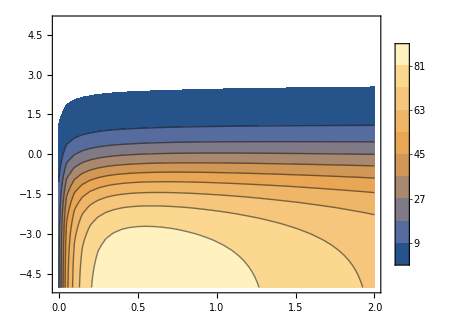

```mathematica
Show[ParametricPlot[-10, {x,0, 30 },PlotRange->{{0, 2},{-5, 5}},
AspectRatio->0.8, Frame->True,FrameStyle->Directive[30]],
ListContourPlot[infoTableTend, PlotLegends->Automatic, DataRange->{{0,2}, {-5, 5}}, PlotRange->{1, 91}, Contours->9]
]
```

```mathematica
infoTableNag[[1, 29]]=31
```

31

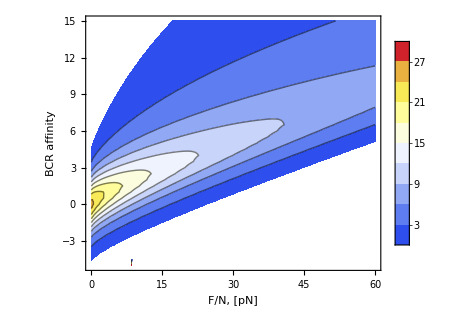

```mathematica
Show[ParametricPlot[-10, {x,0,60 },PlotRange->{{0, 60},{-5, 15}},
AspectRatio->0.8, Frame->True, FrameLabel->{"F/N, [pN]", "BCR affinity"},FrameStyle->Directive[20]],
ListContourPlot[infoTableNag, PlotLegends->Automatic, DataRange->{{0, 60}, {-5, 15}}, PlotRange->{1, 31}, Contours->9, ColorFunction->"TemperatureMap"]]
```

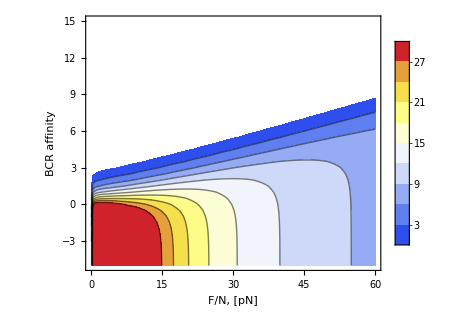

```mathematica
Show[ParametricPlot[-10, {x,0,60 },PlotRange->{{0, 60},{-5, 15}},
AspectRatio->0.8, Frame->True, FrameLabel->{"F/N, [pN]", "BCR affinity"},FrameStyle->Directive[20]],
ListContourPlot[infoTableTend, PlotLegends->Automatic, DataRange->{{0, 60}, {-5, 15}}, PlotRange->{1, 31}, Contours->9, ColorFunction->"TemperatureMap"]]
```

```mathematica
Show[ParametricPlot[-10, {x,0, 60 },PlotRange->{{0, 60},{-5, 15}},
AspectRatio->0.8, Frame->True, FrameLabel->{"F/N, [pN]", "BCR affinity"},FrameStyle->Directive[20]],ContourPlot[If[fx==60, 31,NagFisherInfoIndepF[100, 1, Exp[-ebx],fx]],{fx, 0, 60}, {ebx, -5,15}, PlotLegends->Automatic, PlotRange->{1, 31}, Contours->9,AspectRatio->0.8, Frame->True, FrameLabel->{"F/N, [pN]", "BCR affinity"},FrameStyle->Directive[20], ColorFunction->"TemperatureMap"]]
```

```mathematica
plot1 = ContourPlot[If[fx==60, 31,NagFisherInfoIndepF[100, 1, Exp[-ebx],fx]],{fx, 0, 60}, {ebx, -5,15}, PlotRange->{10, 31}, Contours->9,AspectRatio->0.8,BaseStyle->Directive[Opacity[0.3]],  ColorFunction->"TemperatureMap"]
```

```mathematica
plot2 = ContourPlot[If[fx==60,31,TimeFisherInfoIndepF[100, 1, Exp[-ebx],fx]],{fx, 0, 60}, {ebx, -5,15},  PlotRange->{10, 31}, Contours->9,AspectRatio->0.8,ColorFunction->"TemperatureMap"]
```

```mathematica
Overlay[{plot2, plot1}]
```

```mathematica
Show[ParametricPlot[-10, {x,0, 30 },PlotRange->{{0, 60},{-5, 15}},
AspectRatio->0.8, Frame->True, FrameLabel->{"F/N, [pN]", "BCR affinity"},FrameStyle->Directive[20]],ContourPlot[If[fx==60,31,TimeFisherInfoIndepF[100, 1, Exp[-ebx],fx]],{fx, 0, 60}, {ebx, -5,15}, PlotLegends->Automatic, PlotRange->{1, 31}, Contours->9,AspectRatio->0.8, Frame->True, FrameLabel->{"F/N, [pN]", "BCR affinity"},FrameStyle->Directive[20], ColorFunction->"SolarColors"],
 ContourPlot[If[fx==60, 31,NagFisherInfoIndepF[100, 1, Exp[-ebx],fx]],{fx, 0, 60}, {ebx, -5,15}, PlotRange->{1, 31}, Contours->9,AspectRatio->0.8,ColorFunction->"Aquamarine"]
]
```

#### find maximal point of info per bond

```mathematica
OptimalNIndepF[ka_, kb_, f_, func_]:=ArgMax[{func[n,ka,kb, f/n]/n, n>0, n<1000}, n, Integers];
OptimalN[ka_, kb_, f_, func_]:=ArgMax[{func[n,ka,kb, f]/n, n>0, n<1000}, n, Integers];
OptimalNIndepF[1, 0.01, 500, NagFisherInfoIndepF]
```

14

```mathematica
ArgMax[{NagFisherInfo[n, 1, 1.0Exp[-5], 500]/n, n>1, n<300},n, Integers]
```

20

```mathematica
MakePlotNOpt[ka_, ebx_, func_, i_]:=ListPlot[Table[{fx,OptimalN[ka, 1.0Exp[-ebx]ka,fx, func]}, {fx, 300, 1000, 100}], PlotMarkers->Automatic, PlotStyle->colorlist[[i]]]
MakePlotFNOpt[ka_, fx_, func_, i_]:=ListPlot[Table[{ebx,fx/OptimalNIndepF[ka, 1.0Exp[-ebx]ka,fx, func]}, {ebx,1, 20}], PlotMarkers->Automatic,Joined->True, PlotStyle->colorlist[[i]], PlotRange->{0, 120}]
```

```mathematica
MakePlotNOpt2[ka_, fx_, func_, i_]:=ListLogPlot[Table[{ebx,OptimalN[ka, 1.0Exp[-ebx]ka,fx, func]}, {ebx,1, 20}], PlotMarkers->Automatic, Joined->False,  PlotStyle->colorlist[[i]],PlotRange->{{0,15},{1,500}}]
OptimalNIndepF[1, 1.0Exp[-5],2000, NagFisherInfoIndepF]
```

50

```mathematica
GetDeltaE[f_]:=Module[{},
aTable =Table[{ebx,1/OptimalN[1, 1.0Exp[-ebx],f, NagFisherInfo]}, {ebx,1, 25, 0.5}];
a=Fit[aTable, {1, x}, x]/.x->0;
b=Fit[aTable, {1, x}, x]/.x->1;
{a*f*0.5/4.012, 4.012/(f(b-a))}
]
GetDeltaE[1000]
```

{-2.06211,0.48953}

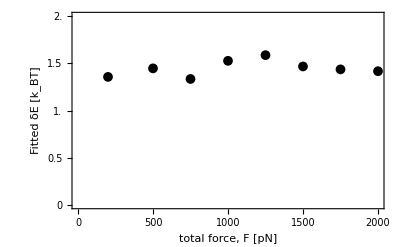

```mathematica
(*Best fit of delta E*)
ListPlot[{{200, 1.35633}, {500, 1.44672}, {750, 1.3343}, {1000, 1.52654}, {1250, 1.58661}, {1500, 1.467}, {1750, 1.436}, {2000, 1.41663}}, PlotRange->{0,2}, Frame->True, PlotStyle->Black,PlotMarkers->{Automatic, 10}, FrameTicks->{{{0, 0.5, 1.0, 1.5, 2.0}, None}, {{0, 500,1000, 1500, 2000}, None}}, FrameLabel->{"total force, F [pN]", "Fitted δE [k_BT]"}, FrameStyle->Directive[15]]
```

```mathematica
f0=500;
bTable = Table[{ebx,(f0*(xb2-xb1)/kT)/OptimalN[1, 1.0Exp[-ebx],f0, NagFisherInfo]}, {ebx,0.3, 15, 0.5}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{0.3,0.0623754},{0.8,0.104728},{1.3,0.333225},{1.8,0.629425},{2.3,0.973642},{2.8,1.35463},{3.3,1.68414},{3.8,2.14873},{4.3,2.59638},{4.8,2.96729},{5.3,3.46184},{5.8,3.89457},{6.3,4.45093},{6.8,4.79331},{7.3,5.19276},{7.8,5.66482},{8.3,6.23131},{8.8,6.92367},{9.3,6.92367},{9.8,7.78913},{10.3,8.90187},{10.8,8.90187},{11.3,8.90187},{11.8,10.3855},{12.3,10.3855},{12.8,10.3855},{13.3,12.4626},{13.8,12.4626},{14.3,12.4626},{14.8,12.4626}}

```mathematica
Fit[aTable, {1, x}, x]
```

-0.0474588+0.0382222 x

```mathematica
0.00911*1000*0.5/4.012
```

1.13534

```mathematica
4.012/(200*0.5)
```

0.04012

```mathematica
Fit[aTable, {1, x}, x]
```

-1.30717+1.02602 x

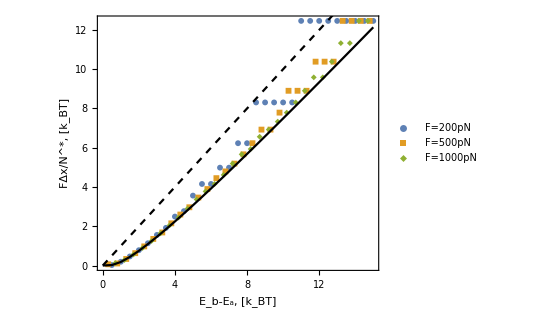

```mathematica
Show[
ListPlot[{aTable, bTable, cTable}, Frame->True,PlotMarkers->{Automatic, 6}, (*FrameTicks->{{{0, 0.1, 0.2}, None}, {{0, 5,10, 15, 20, 25}, None}},*) PlotLegends->Placed[{"F=200pN", "F=500pN", "F=1000pN"}, {0.2, 0.8}],AspectRatio->0.8,FrameLabel->{"E_b-E_a, [k_BT]", "FΔx/N^*, [k_BT]"}, FrameStyle->Directive[25]],
ListPlot[dList,Joined->True, PlotStyle->{Black}],
Plot[x, {x, 0, 16}, PlotStyle->{Black, Dashed}]
(*Plot[-0.014080730644500017+0.007686177879400552 x, {x, 5, 15},Frame->True, PlotStyle->{Red, Thickness[0.01]},*)(*FrameTicks->{{{0, 0.5, 1.0, 1.5}, None}, {{0, 500,1000, 1500, 2000}, None}}, *)]
```

General::munfl: Exp[-788.385] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2764.35] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

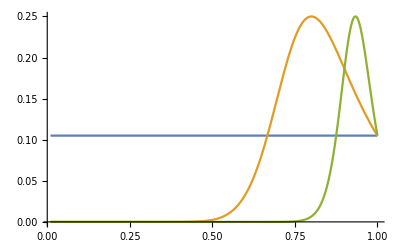

```mathematica
func[u_, eb_, ef_]:=Exp[eb-ef/u]/(1+Exp[eb-ef/u])^2
Plot[{func[u, 2, 0],func[u, 10,10-2],func[u, 30, 30-2]}, {u, 0.01, 1}]
```

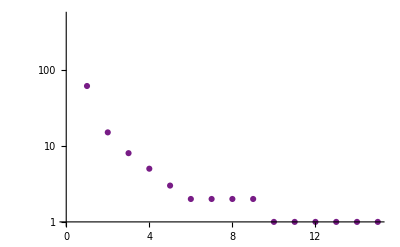

```mathematica
MakePlotNOpt2[1, 100, NagFisherInfo, 1]
```

```mathematica
MakePlotNOptIndepF[ka_, fx_, func_, i_]:=ListLogPlot[Table[{ebx,OptimalNIndepF[ka, 1.0Exp[-ebx]ka,fx, func]}, {ebx,1, 14}], PlotMarkers->Automatic, Joined->False, PlotRange->{1, 500},  PlotStyle->colorlist[[i]]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMaximize::cvdiv will be suppressed during this calculation.

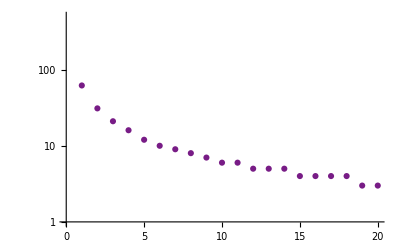

```mathematica
MakePlotNOptIndepF[1, 500, NagFisherInfoIndepF, 1]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

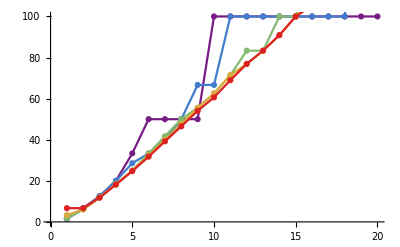

```mathematica
Show[
MakePlotFNOpt[1, 100, NagFisherInfo, 1],
MakePlotFNOpt[1, 200, NagFisherInfo, 2],
MakePlotFNOpt[1, 500, NagFisherInfo, 3],
MakePlotFNOpt[1, 1000, NagFisherInfo, 4],
MakePlotFNOpt[1, 2000, NagFisherInfo, 5]
]
```

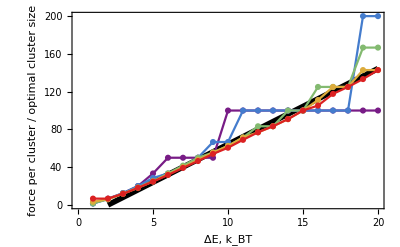

```mathematica
Show[ Plot[(x-2)*4.012/0.5, {x, 0, 20}, PlotStyle->{Black,Thickness[0.01]}, PlotRange->{0, 200}], -Graphics-,Frame->True, FrameLabel->{"ΔE, k_BT", "force per cluster / optimal cluster size"},FrameStyle->Directive[14]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMaximize::cvdiv will be suppressed during this calculation.

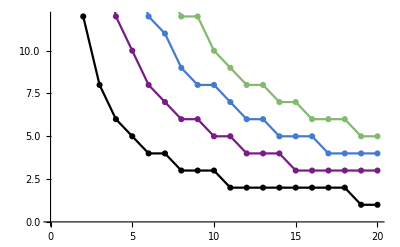

```mathematica
Show[
MakePlotNOpt2[1, 200, NagFisherInfoIndepF, 1],
MakePlotNOpt2[1, 400, NagFisherInfoIndepF, 2],
MakePlotNOpt2[1, 600, NagFisherInfoIndepF, 3],
MakePlotNOpt2[1, 800, NagFisherInfoIndepF, 4]
]
```

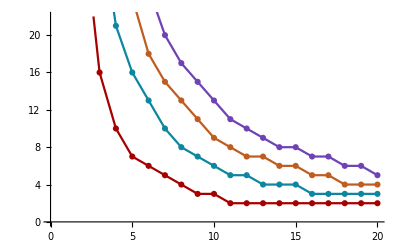

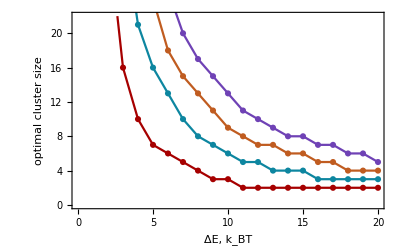

```mathematica
Show[-Graphics-, Frame->True, FrameLabel->{"ΔE, k_BT", "optimal cluster size"},FrameStyle->Directive[14]]
```

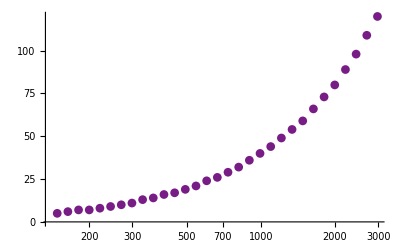
```mathematica
fig2=-Graphics-;
Show[
MakePlotNOpt[1, 3, NagFisherInfo, 1],
MakePlotNOpt[1, 5, NagFisherInfo, 2],
MakePlotNOpt[1, 10, NagFisherInfo, 3],
MakePlotNOpt[1, 15, NagFisherInfo, 4],
Plot[
{x*0.5/(2*4.012),x*0.5/(4*4.012),x*0.5/(9*4.012),x*0.5/(14*4.012) }, {x, 100, 1000}, PlotStyle->colorlist]
]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

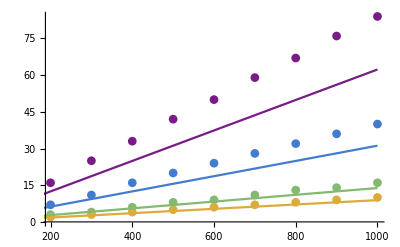

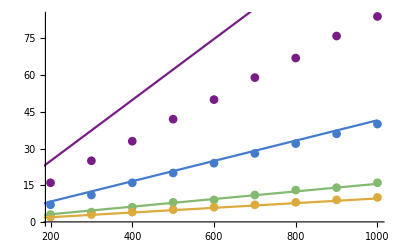
```mathematica
fig2=-Graphics-;
```

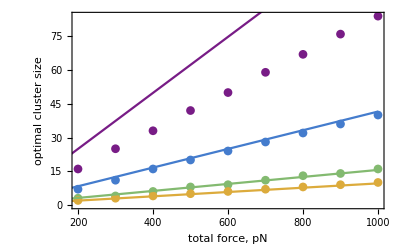

```mathematica
Show[fig2, Frame->True, FrameLabel->{"total force, pN", "optimal cluster size"}, FrameStyle->Directive[13]]
```

```mathematica
Show[
MakePlotNOpt2[1, 200, NagFisherInfo, 1],
MakePlotNOpt2[1, 500, NagFisherInfo, 2],
MakePlotNOpt2[1, 1000, NagFisherInfo, 3],
MakePlotNOpt2[1, 2000, NagFisherInfo, 4],
(*MakePlotNOpt2[1, 2000, NagFisherInfo, 5],*)
(*Plot[(500*0.5)/{x-0.2},{x,1,15}, PlotRange->All], *)
Frame->True,
FrameLabel->{"BCR affinity", "Optimal cluster size"},
LabelStyle->Directive[13]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

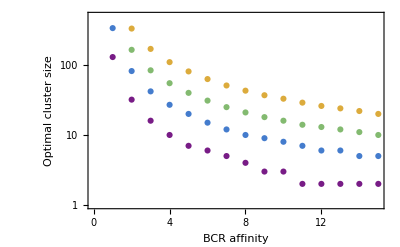
```mathematica
fig0=-Graphics-
```

-Graphics-

```mathematica
analyticalApprox[f_, eb_]:= f*0.5/((eb-deltaE[eb])*4.012);

deltaETable2000 = Table[{x, analyticalApprox[2000, x]}, {x, 0, 15, 0.25}]
```

NIntegrate::inumr: The integrand ⅇ^(0.-Min[100,efx/u])/((1+ⅇ^(0.-Min[100,Times[«2»]]))^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(0.-1. Min[100.,efx/u])/((1.+ⅇ^(0.-1. Min[100.,Times[«1»]]))^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,1.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.000539964}. NIntegrate obtained 0.000123851 and 1.34315×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.,-1.11285×10^17},{0.25,397278.},{0.5,11058.9},{0.75,2920.29},{1.,1376.42},{1.25,829.393},{1.5,569.876},{1.75,424.269},{2.,333.229},{2.25,271.851},{2.5,228.119},{2.75,195.616},{3.,170.645},{3.25,150.94},{3.5,135.045},{3.75,121.985},{4.,111.086},{4.25,101.868},{4.5,93.9811},{4.75,87.1643},{5.,81.2196},{5.25,75.9941},{5.5,71.368},{5.75,67.2465},{6.,63.5533},{6.25,60.2266},{6.5,57.2157},{6.75,54.4787},{7.,51.9808},{7.25,49.6926},{7.5,47.5893},{7.75,45.65},{8.,43.8565},{8.25,42.1933},{8.5,40.6471},{8.75,39.2061},{9.,37.8602},{9.25,36.6005},{9.5,35.4191},{9.75,34.309},{10.,33.2641},{10.25,32.2789},{10.5,31.3486},{10.75,30.4688},{11.,29.6354},{11.25,28.8451},{11.5,28.0946},{11.75,27.3811},{12.,26.7018},{12.25,26.0545},{12.5,25.437},{12.75,24.8472},{13.,24.2835},{13.25,23.744},{13.5,23.2274},{13.75,22.7323},{14.,22.2572},{14.25,21.8011},{14.5,21.3629},{14.75,20.9415},{15.,20.536}}

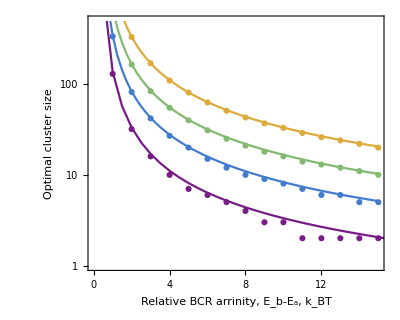

```mathematica
Show[

ListLogPlot[{deltaETable200,deltaETable1000,deltaETable1000s,deltaETable2000
}, PlotRange->{{0, 15},{1, 500}}, PlotStyle->colorlist, Joined->True],
fig0,
Frame->True,
FrameStyle->Directive[20],
FrameTicksStyle->Directive[16],
AspectRatio->0.8,
FrameLabel->{"Relative BCR arrinity, E_b-E_a, k_BT", "Optimal cluster size"}
]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMaximize::cvdiv will be suppressed during this calculation.

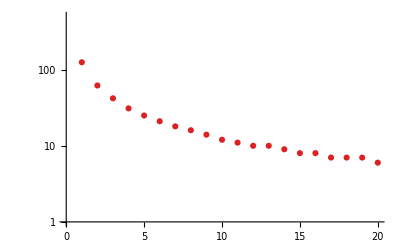

```mathematica
MakePlotNOptIndepF[1, 1000, NagFisherInfoIndepF, 5]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMaximize::cvdiv will be suppressed during this calculation.

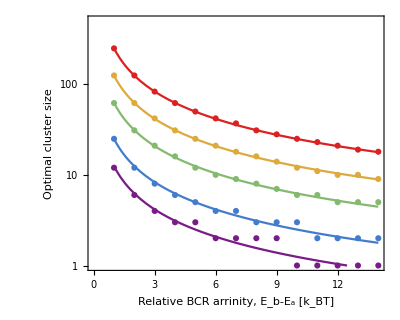

```mathematica
Show[
MakePlotNOptIndepF[1, 2000, NagFisherInfoIndepF, 5],
MakePlotNOptIndepF[1, 100, NagFisherInfoIndepF, 1],
MakePlotNOptIndepF[1, 200, NagFisherInfoIndepF, 2],
MakePlotNOptIndepF[1, 500, NagFisherInfoIndepF, 3],
MakePlotNOptIndepF[1, 1000, NagFisherInfoIndepF, 4],
LogPlot[{analyticalApprox[100, x],analyticalApprox[200, x],analyticalApprox[500, x],analyticalApprox[1000, x],analyticalApprox[2000, x]
},{x,1,14}, PlotRange->{{0, 15},{1, 500}}, PlotStyle->colorlist],
(*Plot[(500*0.5)/{x-0.2},{x,1,15}, PlotRange->All], *)
(*PlotRange->{{0,15},{1,500}},*)
Frame->True,
FrameStyle->Directive[20],
FrameTicksStyle->Directive[16],
AspectRatio->0.8,
FrameLabel->{"Relative BCR arrinity, E_b-E_a [k_BT]", "Optimal cluster size"}]
```

### 2.5 Consider info efficiency, i.e. info / T

```mathematica
TimeFisherInfoEff[n0_,ka_,kb_,F_]:= TimeFisherInfo[n0, ka,kb, F]/TmeanF[n0, ka, kb, F]
NagFisherInfoEff[n0_, ka_, kb_,F_]:=NagFisherInfo[n0, ka, kb, F]/TmeanF[n0, ka, kb, F]
TimeFisherInfoOnEff[n0_, ka_, kb_, kon_]:=TimeFisherInfoOn[n0, ka, kb, kon]/ TmeanOn[n0, ka, kb, kon]
```

```mathematica
MakePlotN[ ka_, kb_, f_,i_, func_]:=Module[{}, ListLogLogPlot[
Table[{n0x, func[n0x, ka, kb, f n0x]/n0x}, {n0x, 1,1000, 2}], PlotStyle->colorlist[[i]], PlotRange->{{1, 1000},{0.1, 100}}, PlotLegends->{f}, Joined->True]]
```

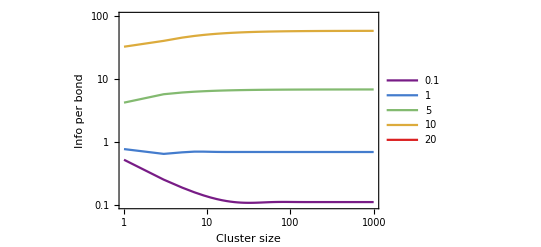

```mathematica
n01= 100;ka1=1; func=TimeFisherInfoEff;
Show[
MakePlotN[ ka1,ka1, 0.1, 1,func],(*change func to TimeFisherInfo to plot curves for time*)
MakePlotN[ ka1,ka1,1, 2, func],
MakePlotN[ ka1, ka1,5, 3, func],
MakePlotN[ ka1, ka1, 10,4, func],
MakePlotN[ ka1, ka1,20, 5, func],
(*MakePlotN[n01, ka1, 0.001ka1, 5, func],*)
Frame->True,
FrameLabel->{"Cluster size", "Info per bond"},
FrameTicksStyle->Directive[12],
FrameStyle->Directive[16]
]
```

### 3. Other plots

#### 3.1 plotting relative std for T and nag

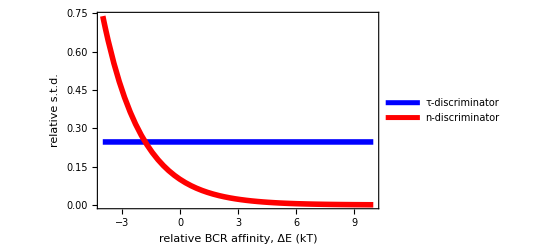

```mathematica
Plot[{Sqrt[TvarF[100,1, Exp[-ebx], 0]]/TmeanF[100,1, Exp[-ebx], 0], Sqrt[nVarF[100,1, Exp[-ebx],0]]/nMeanF[100,1, Exp[-ebx], 0]}, {ebx, -4,10},
PlotStyle->{{Blue, Thickness[0.01]},{Red, Thickness[0.01]}},
PlotLegends->Placed[{"τ-discriminator","n-discriminator"}, {0.7, 0.8}],
Frame->True,
FrameLabel->{"relative BCR affinity, ΔE (kT)", "relative s.t.d."},
FrameStyle->Directive[16],
FrameTicksStyle->Directive[12]]
```

#### 3.2 plot overlapping windows

```mathematica
n01=100;ka1=1;kb1=Exp[-5];f0=20;
IndexTable = {1, 2, 3, 4,5, 7, 9, 11, 15, 20, 25, 30, 35, 39, 40, 45, 50,  60,65, 70, 75, 78, 80,83, 85,87, 100, 99, 98, 97, 96, 95, 94,  92, 90};
(*IndexTable = {2,10, 35, 50,65, 75, 85, 90, 95, 96, 97, 98,99};*)
(*IndexTable = Table[i, {i, 1, 100}]*)
SingleBondBehavior[n0_,ka_, kb_, f_]:=Table[NagFisherInfo[1, ka, kb, f/IndexTable[[i]]],{i, 1, Length[IndexTable]}]
```

```mathematica
SingleBond[n0_, ka_, kb_, f_]:=Table[NagFisherInfo[1, ka, kb, f/i],{i, 1,n0}]
```

General::munfl: 2.36217×10^162 3.06699670828061×10^-427 is too small to represent as a normalized machine number; precision may be lost.

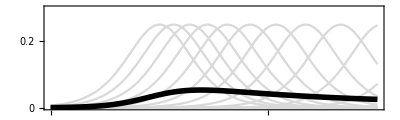

```mathematica
n0=20;
Plot[{SingleBond[n0, 1, Exp[-ebx-2000*0.5/(n0*4.012)], 2000], NagFisherInfo[n0, 1, Exp[-ebx-2000*0.5/(n0*4.012)], 2000]/n0}, {ebx,-5, 10}, Frame->True,PlotRange->{0, 0.3}, FrameStyle->Directive[15],FrameTicks->{{{0, 0.1, 0.2, 0.3}, None}, {{-5, 0, 5, 10, 15, 20}, None}}, AspectRatio->0.3, PlotStyle->{{LightGray}, {Black, Thickness[0.01]}}]
```

General::munfl: 2.36217×10^162 3.66391880705169×10^-434 is too small to represent as a normalized machine number; precision may be lost.

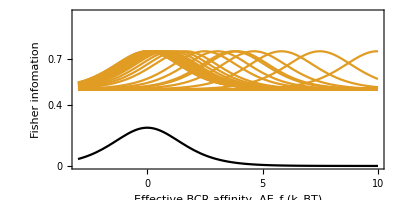

```mathematica
fig2=Show[
Plot[{None, 0.5+SingleBondBehavior[n01, 1, Exp[-kbx-f0*(xb2-xb1)/kT], f0*n01]},{kbx,-3, 10},
PlotRange->{{-3, 10}, {0,1}}, PlotStyle->{Green, Thickness->0.004}],

(*Plot[SingleBondBehavior[n01, 1, Exp[-kbx-(xb2-xb1)/kT],0* n01],{kbx,-3, 10},
PlotRange->{{-3, 10}, {0,1}}, PlotStyle->{Black, Thickness->0.004}],*)
Plot[NagFisherInfo[1, 1,  Exp[-kbx], 0], {kbx, -3, 10}, PlotStyle->Black],
(*LogPlot[NagFisherInfo[n01, 1, Exp[-kbx-f0*(xb2-xb1)/kT], f0*n01], {kbx, -5, 20}, PlotStyle->{Red, Thickness->0.01},
PlotLegends->Placed[{"entire cluster"},{0.78, 0.6}]],*)
(*LogPlot[NagFisherInfoIndepF[n01, 1, Exp[-kbx-f0*(xb2-xb1)/kT], f0], {kbx, -3, 20}, PlotStyle->{Red,Dashed, Thickness->0.007}],*)
(*Plot[1.0, {x,-3, 20}, PlotStyle->Dashed],*)
(*LogPlot[
XinPerfect[n01, ka1,Exp[-kbx], f0*n01], {kbx, -3, 20},  PlotStyle->{Gray, Thickness->0.006}
],
LogPlot[
n01*XinPerfect[1, 1, Exp[-kbx], f0], {kbx, -3, 20}, PlotStyle->{Gray,Dashed, Thickness->0.006}],*)
Frame->True,
AspectRatio->0.5,
FrameLabel->{"Effective BCR affinity, ΔE_f (k_BT)", "Fisher infomation"},
FrameStyle->Directive[14],
FrameTicks->{ {{0, 0.2, 0.4, 0.5, 0.7, 0.9}, None}, {{0,5, 10}, None}}
(*FrameTicks->{{{0.1, 1,2,3,4}, None},{{0, 5,10,15,20}, None}}*)
]
```

### optimal Eb

```mathematica
OptimalEb[ka_,n0_, f_, func_]:=ArgMax[{func[n0,ka,Exp[-eb], f], eb>0, eb<20}, eb];
OptimalEb[1, 20, 200, NagFisherInfo]-200*0.5/(n0*4.012)
```

0.833758

```mathematica
aTable = Table[{nx, OptimalEb[1,nx, 200, NagFisherInfo]-1*200*0.5/(nx*4.012)}, {nx, 10, 200, 5}];
bTable = Table[{nx, OptimalEb[1,nx, 500, NagFisherInfo]-1*500*0.5/(nx*4.012)}, {nx, 10, 200, 5}];
cTable = Table[{nx, OptimalEb[1,nx, 1000, NagFisherInfo]-1*1000*0.5/(nx*4.012)}, {nx, 10, 200, 5}];
```

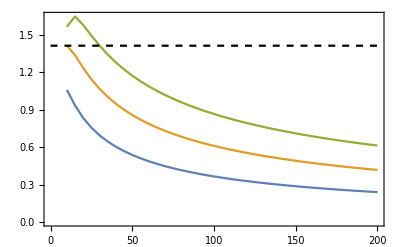

```mathematica
Show[ListPlot[{aTable, bTable, cTable},Joined->True],
Plot[Sqrt[2], {fxx, 0, 200}, PlotStyle->{Dashed, Black}],
Frame->True,
FrameStyle->Directive[Black, 14]
]
```

### scaling relationship

```mathematica
nlist = Join[Table[i, {i, 1, 100}], Table[i, {i, 105, 500, 10}], Table[i, {i, 550, 1000, 50 }]];
```

```mathematica
aTable = Table[{nlist[[i]], TimeFisherInfoIndepF[nlist[[i]], 1, 1,0 nlist[[i]]]}, {i, 1, Length[nlist]}];
bTable = Table[{nlist[[i]], TimeFisherInfo[nlist[[i]], 1, 1,1 nlist[[i]], 1]}, {i, 1, Length[nlist]}];
cTable =Table[{nlist[[i]], TimeFisherInfo[nlist[[i]], 1,1,40 nlist[[i]], 1]}, {i, 1, Length[nlist]}];
```

```mathematica
bTable0 = Table[{nlist[[i]], TimeFisherInfo[nlist[[i]], 1, 1,1nlist[[i]], 0]}, {i, 1, Length[nlist]}];
(*cTable0 = Table[{nlist[[i]], TimeFisherInfo[nlist[[i]], 1, 1,40 nlist[[i]], 0]}, {i, 1, Length[nlist]}];*)
```

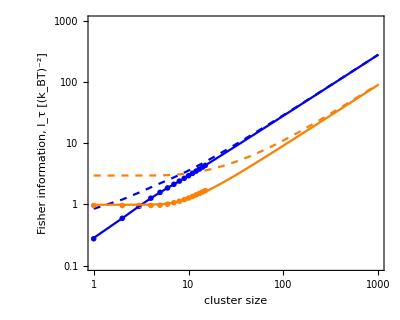

```mathematica
Show[ListLogLogPlot[{
bTable, cTable
}, Joined->True, PlotStyle->{{Dashed, Blue},{Dashed, Orange}},AspectRatio->0.8, PlotRange->{{1, 1000}, {0.1, 1000}}],
ListLogLogPlot[{ infolistT1, infolistT40},PlotStyle->{ Blue, Orange}, PlotMarkers->{{●,Large}, {●,Large}}],

ListLogLogPlot[{
 bTable0, cTable0
}, Joined->True, PlotStyle->{ Blue, Orange},AspectRatio->0.8, PlotRange->{{1, 1000}, {0.1, 1000}}],

Frame->True, FrameLabel->{"cluster size", "Fisher information, I_τ [(k_BT)^-2]"}, FrameStyle->Directive[16]]
```

```mathematica
Sqrt[0.4^2+0.6^2]
```

0.72111

```mathematica
aTable = Table[{nlist[[i]], TimeFisherInfoOn[nlist[[i]], 1, 1, 0]}, {i, 1, Length[nlist]}];
bTable = Table[{nlist[[i]], TimeFisherInfoOn[nlist[[i]], 1, 1, 0.2]}, {i, 1, Length[nlist]}];
cTable =Table[{nlist[[i]], TimeFisherInfoOn[nlist[[i]], 1, 1,1]}, {i, 1, Length[nlist]}];
```

General::munfl: (1.×10^-303)/91809 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.×10^-304)/92416 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.×10^-305)/93025 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

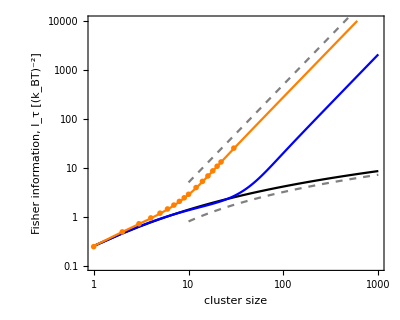

```mathematica
Show[ListLogLogPlot[{
aTable, bTable, cTable
}, Joined->True, PlotStyle->{Black, Blue, Orange},AspectRatio->0.8, PlotRange->{{1, 1000}, {0.1, 10000}}],
ListLogLogPlot[{ {None}, InfoListTon2},PlotStyle->{ Blue, Orange}, PlotMarkers->{{●,Large}, {●,Large}}],
LogLogPlot[{0.15Log[nx]^2}, {nx, 10, 1000}, PlotStyle->{Gray, Dashed}],
LogLogPlot[{0.05nx^2}, {nx, 10, 1000}, PlotStyle->{Gray, Dashed}],
Frame->True, FrameLabel->{"cluster size", "Fisher information, I_τ [(k_BT)^-2]"}, FrameStyle->Directive[16]]
```

```mathematica
aTable = Table[{nlist[[i]],NagFisherInfoIndepF[nlist[[i]], 1, 1,0 nlist[[i]]]}, {i, 1, Length[nlist]}];
bTable = Table[{nlist[[i]], NagFisherInfo[nlist[[i]], 1, 1,10 nlist[[i]]]}, {i, 1, Length[nlist]}];
cTable =Table[{nlist[[i]], NagFisherInfo[nlist[[i]], 1, 1,20 nlist[[i]]]}, {i, 1, Length[nlist]}];
```

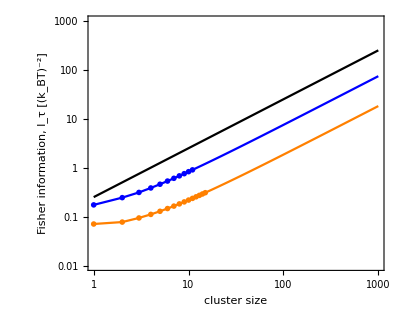

```mathematica
Show[ListLogLogPlot[{
aTable, bTable, cTable
}, Joined->True, PlotStyle->{Black, Blue, Orange},AspectRatio->0.8, PlotRange->{{1, 1000}, {0.01, 1000}}],
(*obtained fromm nag_fisher_info_exact *)
ListLogLogPlot[{ infolistN,infolistN20},PlotStyle->{ Blue, Orange}, PlotMarkers->{{●,Large}, {●,Large}}],
Frame->True, FrameLabel->{"cluster size", "Fisher information, I_τ [(k_BT)^-2]"}, FrameStyle->Directive[16]]
```

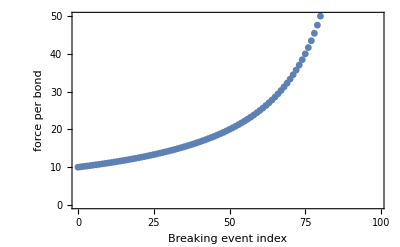

```mathematica
DiscretePlot[1000/(100-i), {i, 0, 99}, PlotRange->{0, 50},

Frame->True,Filling->False,PlotMarkers->{Automatic,Small},
FrameLabel->{"Breaking event index", "force per bond"},
FrameStyle->Directive[15]]
```

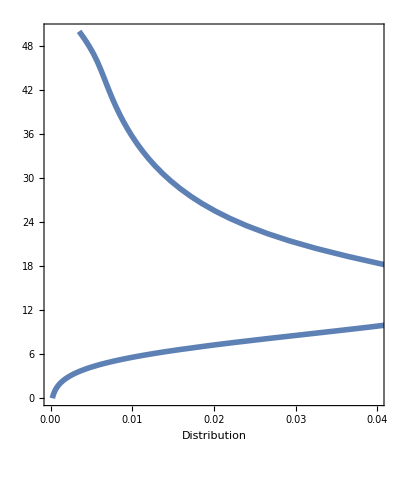

```mathematica
fTable = Table[1000/i, {i, 20, 100}];
ParametricPlot[{PDF[SmoothKernelDistribution[fTable], x], x},{x, 0, 50}, Frame->True, PlotStyle->Thickness[0.01], PlotRange->{{0, 0.04}, {0, 50}}, AspectRatio->1.2,
FrameLabel->{"Distribution"},
FrameStyle->Directive[20]]
```

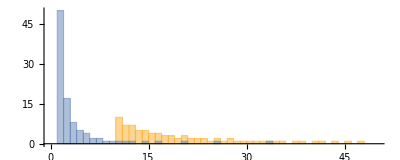

```mathematica
fTable1 = Table[100/i, {i, 1, 100}];
fTable2 = Table[1000/i, {i, 1, 100}];
Histogram[{ fTable2,fTable1}, {Table[i, {i, 0, 50}]}, PlotRange->{{0, 50}, {0, 50}} , AspectRatio->0.4]
```

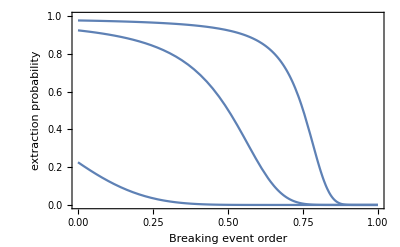

```mathematica
Show[
Plot[1/(1+Exp[-5+1000*0.5/((20-20*i)*4.012)]), {i, 0,1},
PlotRange->{ {0, 1},{0, 1}}],

Plot[1/(1+Exp[-5+1000*0.5/((50-50*i)*4.012)]), {i, 0, 1},
PlotRange->{0, 1}],

Plot[1/(1+Exp[-5+1000*0.5/((100-100*i)*4.012)]), {i, 0, 1},
PlotRange->{0, 1}],


Frame->True,
FrameLabel->{"Breaking event order", "extraction probability"},
FrameStyle->Directive[15]]
```

```mathematica
1000*0.5/(3*4.012)
```

41.542

```mathematica
Integrate[1/(x^n-x),x, Assumptions->{0<x<1, n>2}]
```

```mathematica
D[Log[x^(1-n)-1]/(-1+n), x]
```

((1-n) x^-n)/((-1+n) (-1+x^(1-n)))

```mathematica
Simplify[%]
```

1/(-x+x^n)

```mathematica
Integrate[1/(x^2-x),x]
```

Log[1-x]-Log[x]

```mathematica
Integrate[y Exp[x]/(y+Exp[x/2])^4, {y, 0, Infinity}]
```

ConditionalExpression[1/6, Im[ⅇ^(x/2)]≠0||Re[ⅇ^(x/2)]≥0]

```mathematica
Integrate[1/((y+x1)^2 *(y+x2)), {y,0,Infinity}]
```

ConditionalExpression[(-x1+x2+x1 Log[x1]-x1 Log[x2])/(x1 (x1-x2)^2), (Re[x2]>0||x2∉ℝ)&&(Re[x1]>0||x1∉ℝ)]

```mathematica
pdf[y_, k_, n_]:=n y^(n-1)Exp[k]/(y^n+Exp[k])^2
```

```mathematica
Integrate[pdf[y, k, n], {y, 0, Infinity}, Assumptions->{k>0, n>0, Im[(-1)^(1/n)]≠0}]
```

1

```mathematica
Integrate[pdf[y, k,5], {y, 0, Infinity}, Assumptions->{k>0}]
```

1

```mathematica
Integrate[pdf[y1, k1,3]Integrate[pdf[y2, k2,3],{y2, 0, y1}, Assumptions->{Exp[k2]>0,Re[ⅇ^(k2/2)/y1]≠0}],{y1, 0,Infinity}, Assumptions->{Exp[k1]>0, Exp[k2]>0}]
```

```mathematica
Integrate[ConditionalExpression[(9 ⅇ^(k1+k2) y1^2)/((3 ⅇ^k2+(3 ⅇ^(2 k2))/y1^3) (ⅇ^k1+y1^3)^2), True],{y1,0,∞},Assumptions->{ⅇ^k1>0,ⅇ^k2>0}]
```

ConditionalExpression[(ⅇ^k1 (ⅇ^k1+ⅇ^k2 (-1+Log[ⅇ^(-k1+k2)])))/((ⅇ^k1-ⅇ^k2)^2), ]

```mathematica
Integrate[ConditionalExpression[(4 ⅇ^(k1+k2) y1)/((2 ⅇ^k2+(2 ⅇ^(2 k2))/y1^2) (ⅇ^k1+y1^2)^2), Re[ⅇ^(k2/2)/y1]≠0||Im[ⅇ^(k2/2)/y1]<-1||Im[ⅇ^(k2/2)/y1]>1],{y1,0,∞},Assumptions->{ⅇ^k1>0,ⅇ^k2>0}]
```

```mathematica
Series[(ⅇ^k1 (ⅇ^k1+ⅇ^k2 (-1+Log[ⅇ^(-k1+k2)])))/((ⅇ^k1-ⅇ^k2)^2), {k2, k1, 3}]
```

1/2-(k2-k1)/6+1/180 (k2-k1)^3+O[k2-k1]^4

```mathematica
(ⅇ^k1 (ⅇ^k1-ⅇ^k2+ⅇ^k2 Log[ⅇ^(-k1+k2)]))/((ⅇ^k1-ⅇ^k2)^2)
```

```mathematica
InverseErf
```

```mathematica
s[f_, n_]:=-1-Log[1-f^(1/n)](1-(n-1)(1/f^(1/n) -1))
s[0,n]
```

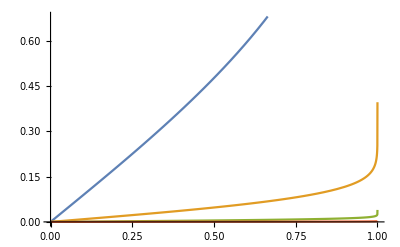

```mathematica
Plot[
{s[fx,1], s[fx,10], s[fx, 100], s[fx,1000]},{fx, 0, 1}]
```

```mathematica
Integrate[s[fx^(1/m), n],{fx, 0, 1}]
```

ConditionalExpression[-1+1/m-((-1+m) n (EulerGamma+PolyGamma[0,m n]))/(1-m n), Re[1/(m n)]>0]

```mathematica
Integrate[s[fx, n]^2,{fx, 0, 1}]
```

ConditionalExpression[(-12+6 n (6-2 EulerGamma (-1+n)^2+EulerGamma^2 (-1+n)^2+(-4+n) n)+(-1+n)^2 n π^2+6 (-1+n)^2 n (PolyGamma[0,n] (-2+2 EulerGamma+PolyGamma[0,n])-PolyGamma[1,-1+n]))/(6 (-2+n) (-1+n)^2), Re[n]>0]

```mathematica
lhs[m_, n_]:=(-1+1/m-((-1+m) n (EulerGamma+PolyGamma[0,m n]))/(1-m n))/m
rhs[m_, n_]:=Sqrt[(1/(6 (-2+n) (-1+n)^2)(-12+6 n (6-2 EulerGamma (-1+n)^2+EulerGamma^2 (-1+n)^2+(-4+n) n)+(-1+n)^2 n π^2+6 (-1+n)^2 n (PolyGamma[0,n] (-2+2 EulerGamma+PolyGamma[0,n])-PolyGamma[1,-1+n])))*(m-1)^2/(m^2(2m-1))]
error[m_, n_]:=(lhs[m, n]-rhs[m, n])/lhs[m, n]
```

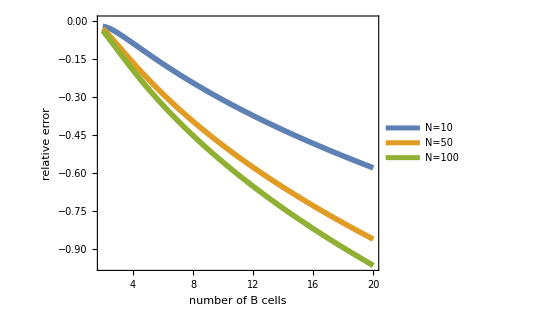

```mathematica
Plot[{ error[mx, 10], error[mx, 50], error[mx, 100]}, {mx, 2, 20}, 
PlotStyle->Thickness[0.01],
PlotLegends->Placed[{"N=10","N=50", "N=100"}, {0.7, 0.8}],
AspectRatio->0.8,
Frame->True,
FrameStyle->Directive[20],
FrameLabel->{"number of B cells", "relative error"}]
```

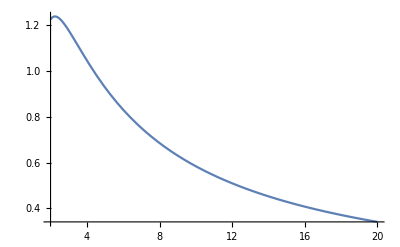

```mathematica
Plot[lhs[mx, 100],{mx, 2, 20}]
```

```mathematica
s[f_, sigma_]:=Sqrt[2]/sigma InverseErf[2f-1]
lhsG[m_, n_]:=NIntegrate[s[fx^(1/m), n],{fx, 0, 1}]/m
rhsG[m_, n_]:= Sqrt[(1/(n^2)) (m-1)^2/(m^2(2m-1))]
```

```mathematica
lhsG[2, 1]-1/(2Sqrt[Pi])
```

1.27676×10^-15

```mathematica
Integrate[(x-mu)^2 normal[x, mu, sigma], {x, -Infinity, Infinity}]
```

ConditionalExpression[√(1/sigma^2) sigma^3, Re[sigma^2]≥0]

```mathematica
Integrate[s[fx^(1/3), n],{fx, 0, 1}]
```

∫_0^1 (√2 InverseErf[-1+2 fx^(1/3)])/n ⅆfx

```mathematica
Integrate[s[fx, n]^2,{fx, 0, 1}]
```

1/n^2

```mathematica
errorG[m_, n_]:=(lhsG[m, n]-rhsG[m, n])/lhsG[m,n]
```

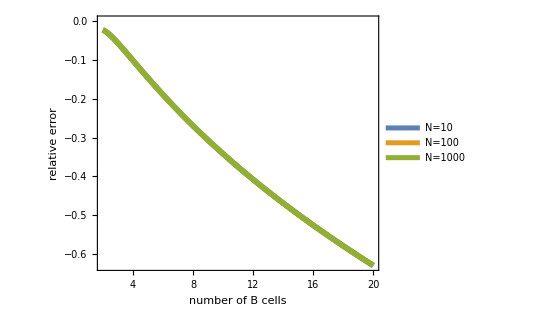

```mathematica
Plot[{ errorG[mx,10], errorG[mx, 50], errorG[mx, 100]}, {mx, 2, 20},
PlotStyle->Thickness[0.01],
PlotLegends->Placed[{"N=10","N=100", "N=1000"}, {0.2, 0.4}],
AspectRatio->0.8,
Frame->True,
FrameStyle->Directive[20],
FrameLabel->{"number of B cells", "relative error"}]
```

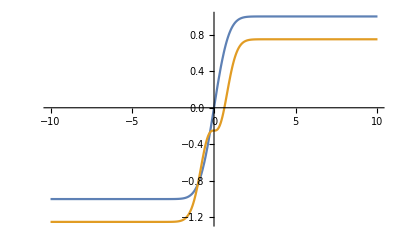

```mathematica
Plot[{Erf[x], Erf[x]^3-1/4},{x, -10, 10}]
```

```mathematica
eta[ eb_]:=1/(1+Exp[-eb])
Clear[fidelityNag, fidelityNagApprox, eb1, n, nB, dE]
fidelityNag[eb1_, n_, nB_:2]:=1.0 Sum[Binomial[n, n0](n0-n eta[eb1])eta[eb1]^n0 (1-eta[eb1])^(n-n0)(Sum[Binomial[n, n1]eta[eb1]^n1 (1-eta[eb1])^(n-n1), {n1, 0, n0-1}])^(nB-1), {n0, 1, n}]
fidelityNagApprox[eb1_, n_, nB_:2]:= (nB-1)/(nB Sqrt[2nB-1])Sqrt[n Exp[eb1]]/(1+Exp[eb1])
```

```mathematica
fidelityNag[0, 100]
fidelityNagApprox[0,  2]
```

1.40871

1/(2 √6)

```mathematica
5/(2 √3)
```

```mathematica
errorN[m_, n_]:=(fidelityNag[0,  n, m]-fidelityNagApprox[0, n, m])/fidelityNag[0,  n, m]
```

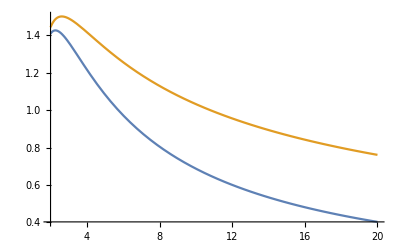

```mathematica
Plot[{fidelityNag[0,  100,nbx], fidelityNagApprox[0, 100,nbx]}, {nbx, 2, 20}]
```

```mathematica
Binomial[2,1]
```

2

```mathematica
1.0 error[2, 1000]
errorN[2, 1000]
errorG[2, 1000]
```

-0.0637845

-0.0234546

-0.0233267

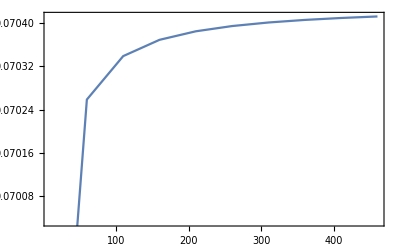

```mathematica
DiscretePlot[{ fidelityNag[0.1, x,2]/Sqrt[x Exp[0]]/(1+Exp[0])},{x, 10, 500, 50}, Filling->False, Joined->True,
Frame->True]
```

```mathematica
coefff[pr_]:=1/12-(1/2-eta[eb])eta[eb]^2-1/3 ((1-eta[eb])^3+eta[eb]^3)-1/4 ((1-eta[eb])^2+eta[eb]^2)^2
coefff[0]
```

-1/16

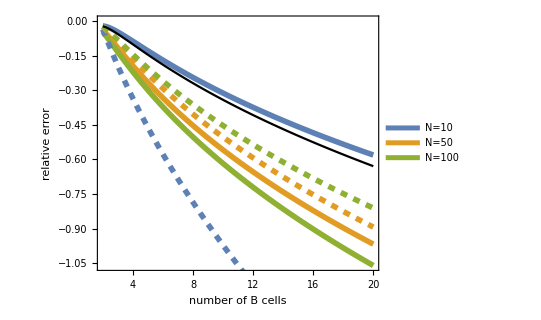

```mathematica
Show[Plot[{ error[mx, 10], error[mx, 100], error[mx, 200]}, {mx, 2, 20}, 
PlotStyle->Thickness[0.01],
PlotLegends->Placed[{"N=10","N=50", "N=100"}, {0.7, 0.8}],
AspectRatio->0.8,
Frame->True,
FrameStyle->Directive[20],
FrameLabel->{"number of B cells", "relative error"}], Plot[{ errorN[mx, 10], errorN[mx, 100], errorN[mx,200]}, {mx, 2, 20}, 
PlotStyle->{
{Dashed,Thickness[0.01]},
{Dashed,Thickness[0.01]},
{Dashed,Thickness[0.01]}
},
(*PlotLegends->Placed[{"N=10","N=50", "N=100"}, {0.8, 0.8}],*)
AspectRatio->0.8,
Frame->True,
FrameStyle->Directive[20],
FrameLabel->{"number of B cells", "relative error"}],
Plot[{ errorG[mx,10]}, {mx, 2, 20},
PlotStyle->Black]]
```

```mathematica
fidelityNag0[eb1_, n_, nB_:2, dE_:0.1]:=Sum[Binomial[n, n0]eta[eb1]^n0 (1-eta[eb1])^(n-n0)(Sum[Binomial[n, n1]eta[eb1-dE]^n1 (1-eta[eb1-dE])^(n-n1), {n1, 0, n0-1}])^(nB-1), {n0, 1, n}]
fidelityNagApprox0[eb1_, n_, nB_:2,dE_:0.1]:=1/nB+ (nB-1)/(nB Sqrt[2nB-1])Sqrt[n Exp[eb1]]/(1+Exp[eb1])*dE+(Sqrt[n Exp[eb1]]/(1+Exp[eb1])*dE)^2
```

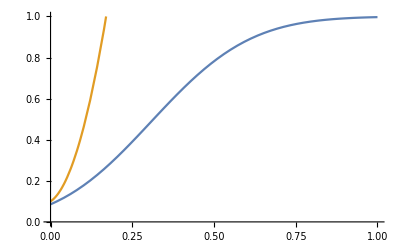

```mathematica
Plot[{fidelityNag0[0,100, 10, ex],
fidelityNagApprox0[0,100,10,ex]
},{ex, 0,1}, PlotRange->{0, 1}]
```

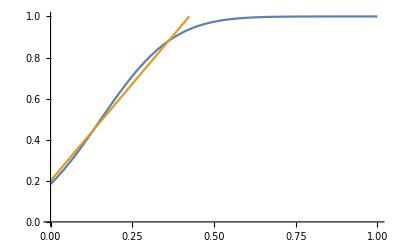

```mathematica
Plot[{fidelityNag0[0,200, 5, ex],
fidelityNagApprox0[0,200,5,ex]
},{ex, 0,1}, PlotRange->{0, 1}]
```

```mathematica
hill[x_, xc_, n_, f0_]:=f0/(1+(xc/x)^n)
```

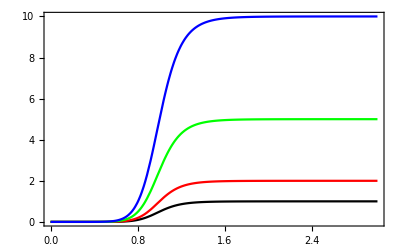

```mathematica
Plot[{
hill[x,1, 10, 1],hill[x, 1,10, 2],hill[x, 1,10, 5],hill[x,1, 10, 10]
},{x, 0,3}, PlotStyle->{Black, Red, Green, Blue},
Frame->True,
FrameStyle->Directive[25]]
```

```mathematica
Clear[prob]
prob[y_, nB_, eb_, a_]:=a/(nB-1) *y^(a/(nB-1)-1)Exp[(nB-1)  eb/(nB)]/(y^a + Exp[(nB-1)eb/nB])^(nB/(nB-1))
```

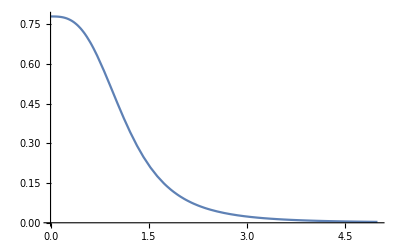

```mathematica
Plot[prob[yx,4, 1,3], {yx, 0, 5}, PlotRange->All]
```

```mathematica
Integrate[prob[t, n, e, a], t]
```

ⅇ^(e (-1+1/n)+(e (-1+n))/n) t^(a/(-1+n)) (ⅇ^((e (-1+n))/n)+t^a)^(1/(1-n))

```mathematica
Simplify[%]
```

t^(a/(-1+n)) (ⅇ^((e (-1+n))/n)+t^a)^(1/(1-n))

```mathematica
fidelityPefect[eb_, nB_, dE_, a_:1]:=NIntegrate[prob[y, nB, eb, a](NIntegrate[prob[y1, nB, eb-dE, a],{y1, 0, y}])^(nB-1), {y, 0, Infinity}]
```

```mathematica
fidelityPefect[0, 10, 0.1]
```

NIntegrate::nlim: y1 = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.104318

NIntegrate::nlim: y1 = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

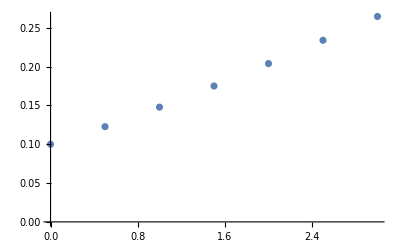

```mathematica
ListPlot[Table[{dex, fidelityPefect[0, 10, dex]}, {dex, 0, 3, 0.5}]]
```

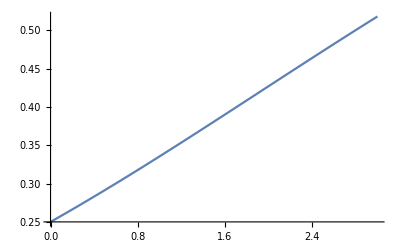

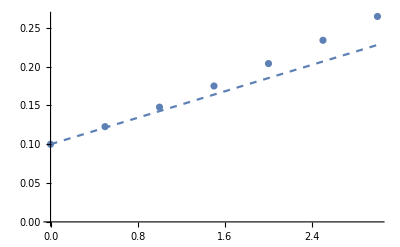

```mathematica
Show[%,
Plot[0.1+(1-1/10)^2 /(2*10-1)x, {x, 0, 3}, PlotStyle->Dashed]]
```

```mathematica
Integrate[y^(a b-1)/(y^a+c)^(b+2), {y, 0, Infinity}]
```

ConditionalExpression[1/(a (b+b^2) c^2), ]

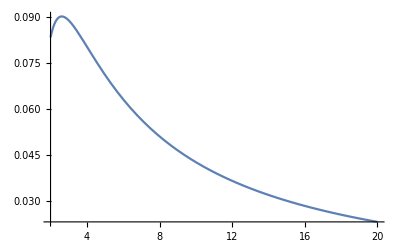

```mathematica
Plot[(1-1/n)^2/(2n-1), {n, 2, 20}]
```

```mathematica
DensityPlot[eta[]]
```

#### antigen number distribution

```mathematica
disN[n_, l0_, t_, t0_]:=Binomial[l0,n]((t/(t+t0))^n) ((t0/(t+t0))^(l0-n))
eta[ta_,tb_, f_]:=1/(1+ta / tb Exp[f*0.5/4.012])
```

```mathematica
antigenNumberProx[s_, n0_,ta_, tb_,F_]:=Module[
{},
Clear[ux,qi, j, u, part1, part2];
qi[j_, ux_]:= eta[ta, tb, F/(n0-j+1)] Exp[ux]/(1-eta[ta, tb, F/(n0-j+1)]+eta[ta, tb, F/(n0-j+1)] Exp[ux]);
u =FindRoot[Sum[qi[j, ux],{j,1, n0}]==s,{ux, 0}][[All, 2]][[1]];

part1 = Product[1-eta[ta, tb, F/(n0-j+1)]+eta[ta, tb, F/(n0-j+1)]Exp[u],{j,1, n0}] Exp[-u s];
part2 = Sqrt[2 Pi Sum[qi[j, u](1-qi[j,u]),{j,1,n0}]];
ret = part1/ part2;
Clear[ux, qi, j, u, part1, part2];
N[ret, 3]
]
```

```mathematica
antigenNumber[s_, n0_, ta_, tb_, F_, tot_:0]:=Module[{},
Clear[ret, toti];
If[s==0, ret=Product[1-eta[ta, tb, F/(n0-j+1)],{j,1,n0}],
{(*else*)
If[s==n0, ret=Product[eta[ta, tb, F/(n0-j+1)],{j,1,n0}],
(*else*)
{
If [tot==0,
toti = Sum[antigenNumberProx[sj,n0,ta, tb, F],{sj,1,n0-1}],
toti = tot];
ret = antigenNumberProx[s, n0, ta, tb, F]*(1-Product[1-eta[ta, tb, F/(n0-j+1)],{j,1,n0}]-Product[eta[ta, tb, F/(n0-j+1)],{j,1,n0}])/toti
}]
}];
ret
]
```

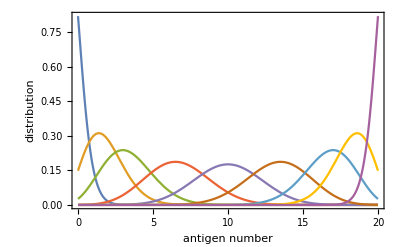

```mathematica
Plot[{
disN[nx, 20, 0.01, 1],
disN[nx, 20, 0.1, 1],
disN[nx, 20, 0.2, 1],
disN[nx, 20,0.5, 1],
disN[nx, 20, 1, 1],
disN[nx, 20, 2, 1],
disN[nx, 20,5, 1],
disN[nx,20, 10, 1],
disN[nx, 20, 100, 1]
}, {nx, 0, 20}, PlotRange->All,PlotStyle->ColorData["Rainbow"][0, 10],
Frame->True, FrameLabel->{"antigen number", "distribution"}, FrameStyle->Directive[20]]
```

```mathematica
DiscretePlot[{
antigenNumber[nx,100,1,1, 10]
}, {nx, 0, 100}, PlotRange->All,PlotStyle->ColorData["Rainbow"][0, 10],
Frame->True, FrameLabel->{"antigen number", "distribution"}, FrameStyle->Directive[20]]
```

$Aborted

```mathematica
antigenNumber[50,100,1,1, 10]
```

0.0758982

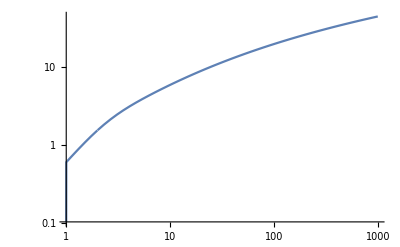

```mathematica
LogLogPlot[TimeFisherInfoIndepF[n0x, 1, 1,10 n0x], {n0x, 1, 1000}]
```